## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]
```

## 设置non-GR参数字符flag

```mathematica
eventFlag="GW150914";
psiFlag="psi";
alphaFlag="alpha";

deviationFlag="fdchi";
deviationOrder="6l";
deviationType="fractional";

alphaName=alphaFlag<>deviationOrder
psiName=psiFlag<>deviationOrder
deviationName=deviationFlag<>deviationOrder
modifiedAlphaName=alphaFlag<>deviationOrder<>deviationFlag
modifiedPsiName=psiFlag<>deviationOrder<>deviationFlag
```

alpha6l

psi6l

fdchi6l

alpha6lfdchi

psi6lfdchi

## Prepare Data from CSV or HDF

```mathematica
csvFolder="D:\\Documents\\workspace\\课题\\workspace\\Parameterized_PN_Tests\\csv"<>"\\"<>eventFlag;
csvName="OGC4-GW150914_"<>deviationName<>".csv";
csvPath=csvFolder<>"\\"<>csvName;
```

### from CSV

```mathematica
CSVSamples=Import[csvPath];

samples=<||>;
samples["mass1"]=CSVSamples[[All,1]][[2;;]];
samples["mass2"]=CSVSamples[[All,2]][[2;;]];
samples["spin1_z"]=CSVSamples[[All,3]][[2;;]];
samples["spin2_z"]=CSVSamples[[All,4]][[2;;]];
samples["eta"]=CSVSamples[[All,5]][[2;;]];
samples["Mchirp"]=CSVSamples[[All,6]][[2;;]];
samples[deviationName]=CSVSamples[[All,7]][[2;;]];
```

```mathematica
samples["chis"]=χs[samples["spin1_z"],samples["spin2_z"]];
samples["chia"]=χa[samples["spin1_z"],samples["spin2_z"]];
```

### Calculate Coefficients

#### N-Order Coefficients, α

```mathematica
samples["alpha2"]=MapThread[
Alpha[2,η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];

samples["alpha3"]=MapThread[
Alpha[3,η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];

samples["alpha4"]=MapThread[
Alpha[4,η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["alpha6"]=MapThread[
Alpha[6,η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["alpha7"]=MapThread[
Alpha[7,η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
```

#### N-Order Log Coefficients, α

```mathematica
samples["alpha5l"]=MapThread[
Alpha["5l",η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["alpha6l"]=MapThread[
Alpha["6l",η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["alpha8l"]=MapThread[
Alpha["8l",η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
```

#### N-Order Coefficients, Modified α

```mathematica
samples[modifiedAlphaName]=samples[alphaName](1+samples[deviationName]);
```

#### N-Order Coefficients, ψ

```mathematica
samples["psi0"]=MapThread[
LALSimPhi[0,η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi2"]=MapThread[
LALSimPhi[2,η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi6l"]=MapThread[
LALSimPhi["6l",η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
```

#### N-Order Coefficients, ψ

```mathematica
samples[deviationFlag]=MapThread[
LALSimPhi[deviationOrder,η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
```

#### N-Order log Coefficients, Modified ψ

```mathematica
samples[modifiedPsiName]=samples[psiName](1+samples[deviationName]);
```

```mathematica
Keys[samples]
```

{mass1,mass2,spin1_z,spin2_z,eta,Mchirp,fdchi6l,alpha2,alpha3,alpha4,alpha6,alpha7,alpha5l,alpha6l,alpha8l,psi0,psi2,psi6l,fdchi,psi6lfdchi,chis,chia,alpha6lfdchi}

## Plot PN Coefficients and Related Parameters

```mathematica
BCI=<||>;
```

### Plots Masses

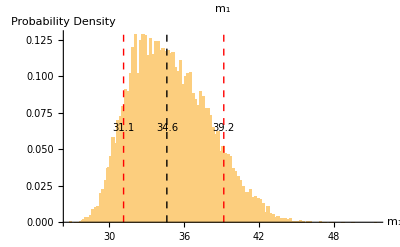

```mathematica
BCI["mass1"]=PlotParameterWithBCI[samples["mass1"],Subscript["m","1"]][[1]];
```

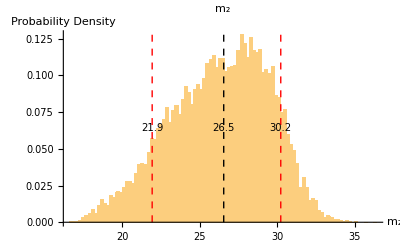

```mathematica
BCI["mass2"]=PlotParameterWithBCI[samples["mass2"],Subscript["m","2"]][[1]];
```

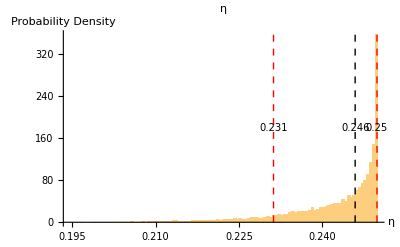

```mathematica
BCI["eta"]=PlotParameterWithBCI[samples["eta"],"η"][[1]];
```

### Plots Spin Components Aligning Orbital Angular Momentum (Then be it spin_z)

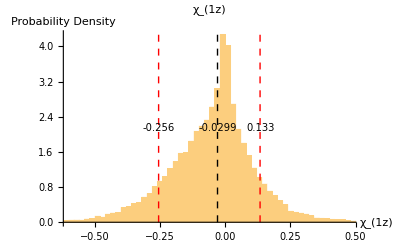

```mathematica
BCI["spin1_z"]=PlotParameterWithBCI[samples["spin1_z"],Subscript["χ","1z"]][[1]];
```

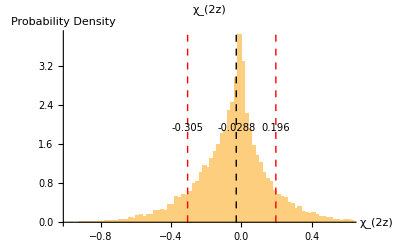

```mathematica
BCI["spin2_z"]=PlotParameterWithBCI[samples["spin2_z"],Subscript["χ","2z"]][[1]];
```

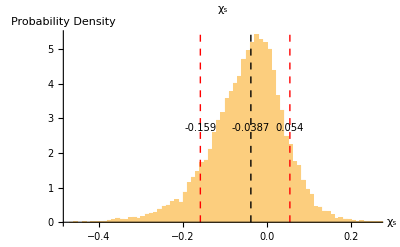

```mathematica
BCI["chis"]=PlotParameterWithBCI[samples["chis"],Subscript["χ","s"]][[1]];
```

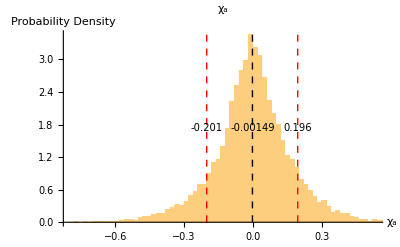

```mathematica
BCI["chia"]=PlotParameterWithBCI[samples["chia"],Subscript["χ","a"]][[1]];
```

### Plot N-Order Coefficients

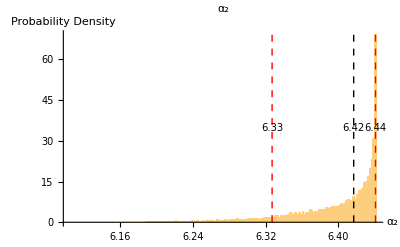

```mathematica
BCI["alpha2"]=PlotParameterWithBCI[samples["alpha2"],Subscript["α","2"]][[1]];
```

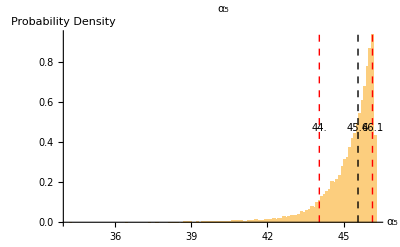

```mathematica
BCI["alpha5"]=PlotParameterWithBCI[samples["alpha4"],Subscript["α","5"]][[1]];
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

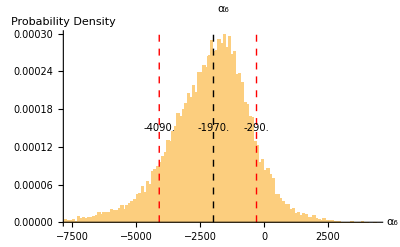

```mathematica
BCI["alpha6"]=PlotParameterWithBCI[samples["alpha6"],Subscript["α","6"]][[1]];
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

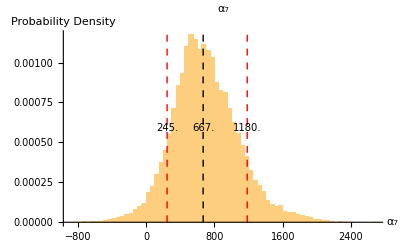

```mathematica
BCI["alpha7"]=PlotParameterWithBCI[samples["alpha7"],Subscript["α","7"]][[1]];
```

### Plot N-Order Log Coefficients

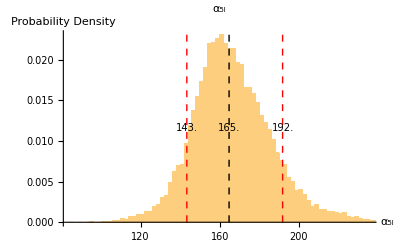

```mathematica
BCI["alpha5l"]=PlotParameterWithBCI[samples["alpha5l"],Subscript["α","5l"]][[1]];
```

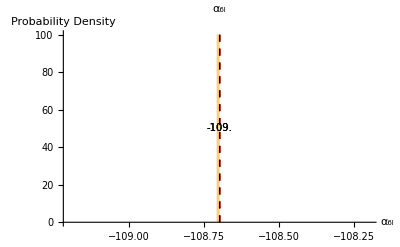

```mathematica
BCI["alpha6l"]=PlotParameterWithBCI[samples["alpha6l"],Subscript["α","6l"]][[1]];
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

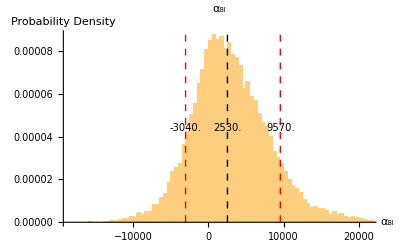

```mathematica
BCI["alpha8l"]=PlotParameterWithBCI[samples["alpha8l"],Subscript["α","8l"]][[1]];
```

### Plot psi

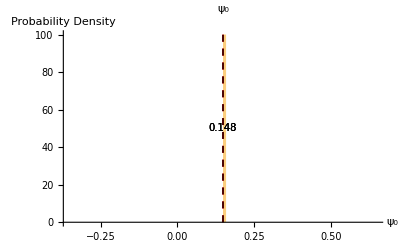

```mathematica
BCI["psi0"]=PlotParameterWithBCI[samples["psi0"],Subscript["ψ","0"]][[1]];
```

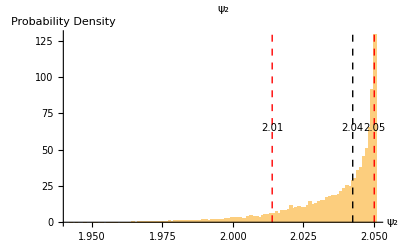

```mathematica
BCI["psi2"]=PlotParameterWithBCI[samples["psi2"],Subscript["ψ","2"]][[1]];
```

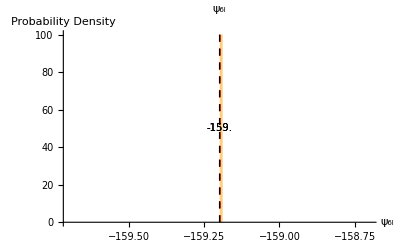

```mathematica
BCI["psi6l"]=PlotParameterWithBCI[samples["psi6l"],Subscript["ψ","6l"]][[1]];
```

### Plot Freedom-Released Coefficients

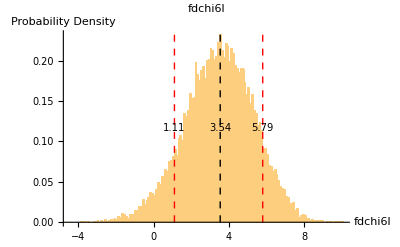

```mathematica
BCI[deviationName]=PlotParameterWithBCI[samples[deviationName],deviationName][[1]];
```

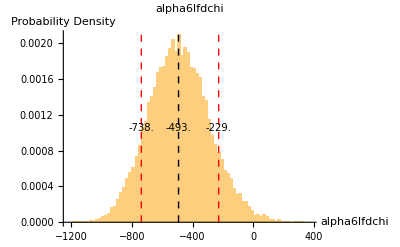

```mathematica
BCI[modifiedAlphaName]=PlotParameterWithBCI[samples[modifiedAlphaName],modifiedAlphaName][[1]];
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

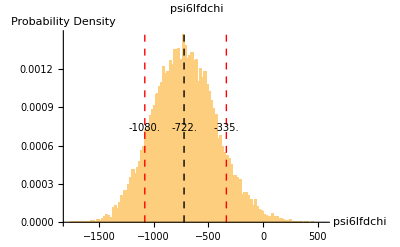

```mathematica
BCI[modifiedPsiName]=PlotParameterWithBCI[samples[modifiedPsiName],modifiedPsiName][[1]];
```

## Calculate Dots

### 2D, m_1-m_2, Fix two spin parameters

#### Set m_2-m_1 Axis

```mathematica
m2s=Range[BCI["mass2"][[1]],BCI["mass2"][[3]],0.1];
m1s=Range[BCI["mass1"][[1]],BCI["mass1"][[3]],0.1];
```

```mathematica
Plot3D[
Function[{m1,m2},LALSimPhi[deviationOrder,η[m1,m2],BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]]][m1,m2],
{m1,BCI["mass1"][[1]],BCI["mass1"][[3]]},
{m2,BCI["mass1"][[1]],BCI["mass1"][[3]]},
PlotPoints->{120,120},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=158.7,Red,Blue]&),
ColorFunctionScaling->False
]
```

-Graphics3D-

```mathematica
BCI["psi6l"]
```

{-159.199,-159.199,-159.199}

#### ψ_0 and ψ_2 Pancakes

```mathematica
pancakes=<||>
```

<||>

```mathematica
pancakes["psi0"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},LALSimPhi[l,η[m1,m2],χ1L,χ2L]],
BCI["psi0"],{m2s},{2},{0,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {h} = {21.9326}.

Part::partw: Part 2 of {True} does not exist.

FindRoot::srect: Value {True}⟦2⟧ in search specification {h,{True}⟦2⟧} is not a number or array of numbers.

Part::partw: Part 2 of {True} does not exist.

FindRoot::srect: Value {True}⟦2⟧ in search specification {h,{True}⟦2⟧} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

Part::partw: Part 2 of {True} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {h} = {26.546}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

```mathematica
pancakes["psi2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},LALSimPhi[l,η[m1,m2],χ1L,χ2L]],
BCI["psi2"],{m2s},{2},{2,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

```mathematica
pancakes[psiName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},LALSimPhi[l,η[m1,m2],χ1L,χ2L]],
BCI[psiName],{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {h} = {21.9326}.

Part::partw: Part 2 of {True} does not exist.

FindRoot::srect: Value {True}⟦2⟧ in search specification {h,{True}⟦2⟧} is not a number or array of numbers.

Part::partw: Part 2 of {True} does not exist.

FindRoot::srect: Value {True}⟦2⟧ in search specification {h,{True}⟦2⟧} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

Part::partw: Part 2 of {True} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {h} = {26.546}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

#### ψ_0 and ψ_2 Non-GR Pancakes

```mathematica
BCI[modifiedPsiName]
```

{-1081.48,-722.309,-335.383}

```mathematica
pancakes[modifiedPsiName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},LALSimPhi[l,η[m1,m2],χ1L,χ2L]],
BCI[modifiedPsiName],{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {h} = {21.9326}.

Part::partw: Part 2 of {False} does not exist.

FindRoot::srect: Value {False}⟦2⟧ in search specification {h,{False}⟦2⟧} is not a number or array of numbers.

Part::partw: Part 2 of {False} does not exist.

FindRoot::srect: Value {False}⟦2⟧ in search specification {h,{False}⟦2⟧} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

Part::partw: Part 2 of {False} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {h} = {26.546}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

```mathematica
pancakes[psiName<>"1e-1"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},LALSimPhi[l,η[m1,m2],χ1L,χ2L]],
BCI[psiName](1+0.1),{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {h} = {21.9326}.

Part::partw: Part 2 of {False} does not exist.

FindRoot::srect: Value {False}⟦2⟧ in search specification {h,{False}⟦2⟧} is not a number or array of numbers.

Part::partw: Part 2 of {False} does not exist.

FindRoot::srect: Value {False}⟦2⟧ in search specification {h,{False}⟦2⟧} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

Part::partw: Part 2 of {False} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {h} = {26.546}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

```mathematica
pancakes[psiName<>"1e-2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},LALSimPhi[l,η[m1,m2],χ1L,χ2L]],
BCI[psiName](1+0.01),{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {h} = {21.9326}.

Part::partw: Part 2 of {False} does not exist.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {h} = {21.9326}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Part::partw: Part 2 of {False} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

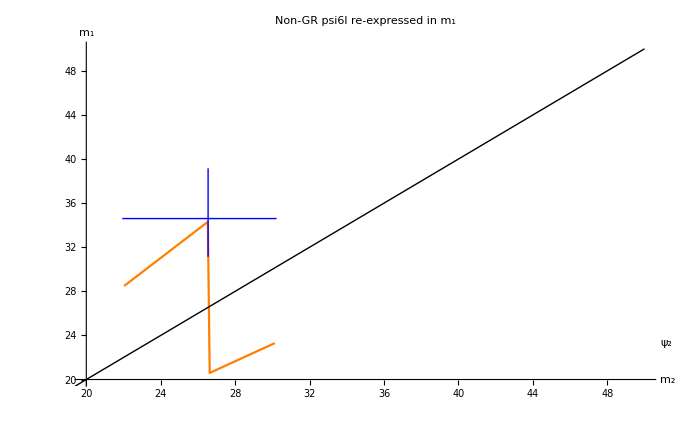

```mathematica
ListLinePlot[
{
Labeled[pancakes["psi0"][[2]][[2;;]],Subscript["ψ","0"]],
Labeled[pancakes["psi2"][[2]][[2;;]],Subscript["ψ","2"]],
Labeled[pancakes[psiName][[2]][[2;;]],psiName],

Labeled[pancakes[psiName<>"1e-2"][[2]][[2;;]],psiName<>"1e-2"],

Labeled[pancakes[psiName<>"1e-1"][[2]][[2;;]],psiName<>"1e-1"],

Labeled[pancakes[modifiedPsiName][[1]][[2;;]],psiName<>" 10% BCI, observed"],
Labeled[pancakes[modifiedPsiName][[2]][[2;;]],psiName<>" 50% BCI, observed"],
Labeled[pancakes[modifiedPsiName][[3]][[2;;]],psiName<>" 90% BCI, observed"]
},
PlotStyle->{Red,Orange,Green,Gray,Gray,Purple,Purple,Purple},
Epilog->{
Blue,Line[{{BCI["mass2"][[2]],BCI["mass1"][[1]]},{BCI["mass2"][[2]],BCI["mass1"][[3]]}}],
Blue,Line[{{BCI["mass2"][[1]],BCI["mass1"][[2]]},{BCI["mass2"][[3]],BCI["mass1"][[2]]}}],
Black,Line[{{0,0},{50,50}}]
	},
PlotLabel->"Non-GR "<>psiName<>" re-expressed in "Subscript["m","1"],
AxesLabel->{Subscript["m","2"],Subscript["m","1"]},
PlotRange->{{20,50},{20,50}}
]
```

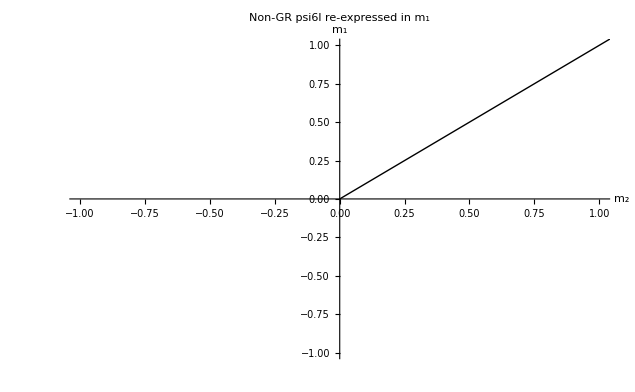

```mathematica
ListLinePlot[
{
Labeled[pancakes[modifiedPsiName][[1]][[2;;]],psiName<>" 10% BCI, observed"],
Labeled[pancakes[modifiedPsiName][[2]][[2;;]],psiName<>" 50% BCI, observed"],
Labeled[pancakes[modifiedPsiName][[3]][[2;;]],psiName<>" 90% BCI, observed"]
},
PlotStyle->{Purple},
Epilog->{
Blue,Line[{{BCI["mass2"][[2]],BCI["mass1"][[1]]},{BCI["mass2"][[2]],BCI["mass1"][[3]]}}],
Blue,Line[{{BCI["mass2"][[1]],BCI["mass1"][[2]]},{BCI["mass2"][[3]],BCI["mass1"][[2]]}}],
Black,Line[{{0,0},{50,50}}]
	},
PlotLabel->"Non-GR "<>psiName<>" re-expressed in "Subscript["m","1"],
AxesLabel->{Subscript["m","2"],Subscript["m","1"]}
]
```

#### ψ_0 and ψ_2 Pancakes, but over m_1-m_2 axis

```mathematica
(* FindRoot寻根，多值性的问题 *)
```

```mathematica
pancakesNew=<||>;
```

```mathematica
pancakesNew["psi0"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI["psi0"],{m1s},{2},{0,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],3];
```

```mathematica
pancakesNew["psi2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI["psi2"],{m1s},{2},{2,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],3];
```

```mathematica
pancakesNew[psiName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName],{m1s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],3];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

#### ψ_0 and ψ_2 Non-GR Pancakes, but over m_1-m_2 axis

```mathematica
pancakesNew[modifiedPsiName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[modifiedPsiName],{m1s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],3];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakesNew[psiName<>"1e-1"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName](1+0.1),{m1s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],3];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakesNew[psiName<>"1e-2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName](1+0.01),{m1s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],3];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

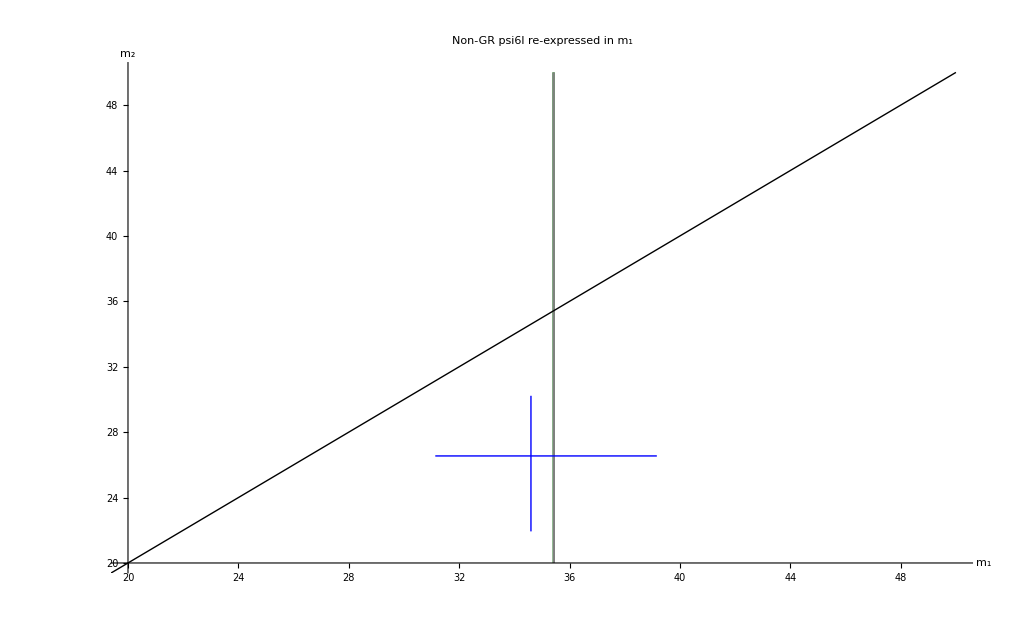

```mathematica
ListLinePlot[
{
Labeled[pancakesNew["psi0"][[2]][[2;;]],Subscript["ψ","0"]],
Labeled[pancakesNew["psi2"][[2]][[2;;]],Subscript["ψ","2"]],
Labeled[pancakesNew[psiName][[2]][[2;;]],psiName],

Labeled[pancakesNew[psiName<>"1e-2"][[2]][[2;;]],psiName<>"1e-2"],

Labeled[pancakesNew[psiName<>"1e-1"][[2]][[2;;]],psiName<>"1e-1"]
},
PlotStyle->{Red,Orange,Green,Gray,Gray,Purple,Purple,Purple},
Epilog->{
Blue,Line[{{BCI["mass1"][[2]],BCI["mass2"][[1]]},{BCI["mass1"][[2]],BCI["mass2"][[3]]}}],
Blue,Line[{{BCI["mass1"][[1]],BCI["mass2"][[2]]},{BCI["mass1"][[3]],BCI["mass2"][[2]]}}],
Black,Line[{{0,0},{50,50}}]
	},
PlotLabel->"Non-GR "<>psiName<>" re-expressed in "Subscript["m","1"],
AxesLabel->{Subscript["m","1"],Subscript["m","2"]},
PlotRange->{{20,50},{20,50}}
]
```

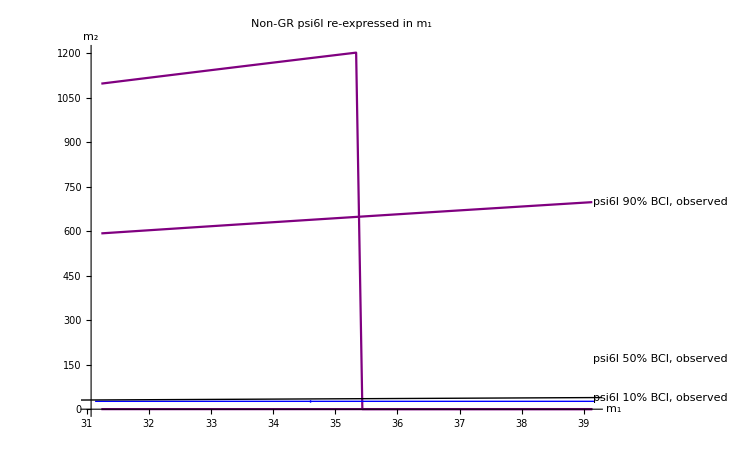

```mathematica
ListLinePlot[
{
Labeled[pancakesNew[modifiedPsiName][[1]][[2;;]],psiName<>" 10% BCI, observed"],
Labeled[pancakesNew[modifiedPsiName][[2]][[2;;]],psiName<>" 50% BCI, observed"],
Labeled[pancakesNew[modifiedPsiName][[3]][[2;;]],psiName<>" 90% BCI, observed"]
},
PlotStyle->{Purple},
Epilog->{
Blue,Line[{{BCI["mass1"][[2]],BCI["mass2"][[1]]},{BCI["mass1"][[2]],BCI["mass2"][[3]]}}],
Blue,Line[{{BCI["mass1"][[1]],BCI["mass2"][[2]]},{BCI["mass1"][[3]],BCI["mass2"][[2]]}}],
Black,Line[{{0,0},{50,50}}]
	},
PlotLabel->"Non-GR "<>psiName<>" re-expressed in "Subscript["m","1"],
AxesLabel->{Subscript["m","1"],Subscript["m","2"]}
]
```

### 3D, χ_s-χ_a-η

```mathematica
chiss=Range[BCI["chis"][[1]],BCI["chis"][[2]],1/10];
chias=Range[BCI["chia"][[1]],BCI["chia"][[2]],1/10];
```

```mathematica
(* alpha_6l是 constant *)
```

```mathematica
pancakes[alphaName]=HypersurfacePancake[
Function[{j,eta,chis,chia},
Alpha[j,eta,χ1L[chis,chia],χ2L[chis,chia]]],(* F_ *)
BCI[alphaName],(* F0_ *)
{chiss,chias},{2,3},(* axes_,axesIndices_ *)
{deviationOrder},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
]
```

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {h} = {0.231222}.

Part::partw: Part 2 of {True} does not exist.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {h} = {0.231222}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Part::partw: Part 2 of {True} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{{{-0.158845,-0.201124,{True}⟦2⟧},{-0.158845,-0.101124,{True}⟦2⟧}},{{-0.0588448,-0.201124,{True}⟦2⟧},{-0.0588448,-0.101124,{True}⟦2⟧}}},{{{-0.158845,-0.201124,{True}⟦2⟧},{-0.158845,-0.101124,{True}⟦2⟧}},{{-0.0588448,-0.201124,{True}⟦2⟧},{-0.0588448,-0.101124,{True}⟦2⟧}}},{{{-0.158845,-0.201124,{True}⟦2⟧},{-0.158845,-0.101124,{True}⟦2⟧}},{{-0.0588448,-0.201124,{True}⟦2⟧},{-0.0588448,-0.101124,{True}⟦2⟧}}}}

```mathematica
HypersurfacePancake[
Function[{j,eta,chis,chia},
Alpha[j,eta,χ1L[chis,chia],χ2L[chis,chia]]],(* F_ *)
BCI[alphaName],(* F0_ *)
{chiss,chias},{2,3},(* axes_,axesIndices_ *)
{deviationOrder},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
]
```

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {h} = {0.231222}.

Part::partw: Part 2 of {True} does not exist.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {h} = {0.231222}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Part::partw: Part 2 of {True} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{{{-0.158845,-0.201124,{True}⟦2⟧},{-0.158845,-0.101124,{True}⟦2⟧}},{{-0.0588448,-0.201124,{True}⟦2⟧},{-0.0588448,-0.101124,{True}⟦2⟧}}},{{{-0.158845,-0.201124,{True}⟦2⟧},{-0.158845,-0.101124,{True}⟦2⟧}},{{-0.0588448,-0.201124,{True}⟦2⟧},{-0.0588448,-0.101124,{True}⟦2⟧}}},{{{-0.158845,-0.201124,{True}⟦2⟧},{-0.158845,-0.101124,{True}⟦2⟧}},{{-0.0588448,-0.201124,{True}⟦2⟧},{-0.0588448,-0.101124,{True}⟦2⟧}}}}

```mathematica
Alpha["6l",0.1,χ1L[0.1,0.2],χ2L[0.1,0.2]]
```

-108.698

```mathematica
BCI[alphaName]
```

{-108.698,-108.698,-108.698}

```mathematica
Thread[Select[pancakes["alpha3"]["GR"],Im[#[[3]]]==0 &]]
```

Part::partd: Part specification GR⟦3⟧ is longer than depth of object.

{{{{-0.176261,-0.258666,0.250014-8.92227×10^-10 ⅈ},{-0.176261,-0.238666,0.250017-1.06325×10^-9 ⅈ},{-0.176261,-0.218666,0.25002-1.28407×10^-9 ⅈ},{-0.176261,-0.198666,0.250024-1.57496×10^-9 ⅈ},{-0.176261,-0.178666,0.25003-1.96706×10^-9 ⅈ},{-0.176261,-0.158666,0.250038-2.50963×10^-9 ⅈ},{-0.176261,-0.138666,0.25005-3.28242×10^-9 ⅈ},{-0.176261,-0.118666,0.250068-4.41452×10^-9 ⅈ},{-0.176261,-0.0986662,0.2501-6.09154×10^-9 ⅈ},{-0.176261,-0.0786662,0.250158-8.33592×10^-9 ⅈ},{-0.176261,-0.0586662,0.250292-7.81962×10^-9 ⅈ},{-0.176261,-0.0386662,0.250715-4.24731×10^-8 ⅈ}},{{-0.156261,-0.258666,0.249412-2.92914×10^-20 ⅈ},{-0.156261,-0.238666,0.24931+4.48509×10^-17 ⅈ},{-0.156261,-0.218666,0.24918-1.01931×10^-24 ⅈ},{-0.156261,-0.198666,0.249009+4.79794×10^-19 ⅈ},{-0.156261,-0.178666,0.24878-2.27772×10^-21 ⅈ},{-0.156261,-0.158666,0.248461+2.15754×10^-21 ⅈ},{-0.156261,-0.138666,0.248001-4.9731×10^-18 ⅈ},{-0.156261,-0.118666,0.247302-1.51083×10^-26 ⅈ},{-0.156261,-0.0986662,0.246172+4.15036×10^-19 ⅈ},{-0.156261,-0.0786662,0.244183},{-0.156261,-0.0586662,0.240249},{-0.156261,-0.0386662,0.231118}},{{-0.136261,-0.258666,0.246866+5.27156×10^-16 ⅈ},{-0.136261,-0.238666,0.246331+1.79127×10^-17 ⅈ},{-0.136261,-0.218666,0.245648-5.30795×10^-19 ⅈ},{-0.136261,-0.198666,0.244758},{-0.136261,-0.178666,0.243568},{-0.136261,-0.158666,0.241929},{-0.136261,-0.138666,0.239592},{-0.136261,-0.118666,0.236106},{-0.136261,-0.0986662,0.230619},{-0.136261,-0.0786662,0.221365},{-0.136261,-0.0586662,0.204363},{-0.136261,-0.0386662,0.16981}},{{-0.116261,-0.258666,0.242337},{-0.116261,-0.238666,0.241039},{-0.116261,-0.218666,0.239386},{-0.116261,-0.198666,0.237238},{-0.116261,-0.178666,0.234377},{-0.116261,-0.158666,0.230461},{-0.116261,-0.138666,0.224916},{-0.116261,-0.118666,0.216738},{-0.116261,-0.0986662,0.204065},{-0.116261,-0.0786662,0.183205},{-0.116261,-0.0586662,0.146329},{-0.116261,-0.0386662,0.0758742}},{{-0.0962614,-0.258666,0.23582},{-0.0962614,-0.238666,0.233427},{-0.0962614,-0.218666,0.230384},{-0.0962614,-0.198666,0.226433},{-0.0962614,-0.178666,0.221185},{-0.0962614,-0.158666,0.21402},{-0.0962614,-0.138666,0.203912},{-0.0962614,-0.118666,0.18908},{-0.0962614,-0.0986662,0.166268},{-0.0962614,-0.0786662,0.129137},{-0.0962614,-0.0586662,0.0646103},{-0.0962614,-0.0386662,-0.0555022}},{{-0.0762614,-0.258666,0.227271},{-0.0762614,-0.238666,0.223437},{-0.0762614,-0.218666,0.218558},{-0.0762614,-0.198666,0.212228},{-0.0762614,-0.178666,0.203818},{-0.0762614,-0.158666,0.192336},{-0.0762614,-0.138666,0.17614},{-0.0762614,-0.118666,0.152381},{-0.0762614,-0.0986662,0.115841},{-0.0762614,-0.0786662,0.0563859},{-0.0762614,-0.0586662,-0.0468903},{-0.0762614,-0.0386662,-0.239007}},{{-0.0562614,-0.258666,0.216609},{-0.0562614,-0.238666,0.210956},{-0.0562614,-0.218666,0.203755},{-0.0562614,-0.198666,0.194397},{-0.0562614,-0.178666,0.181941},{-0.0562614,-0.158666,0.164892},{-0.0562614,-0.138666,0.140759},{-0.0562614,-0.118666,0.105182},{-0.0562614,-0.0986662,0.0500815},{-0.0562614,-0.0786662,-0.0405277},{-0.0562614,-0.0586662,-0.200478},{-0.0562614,-0.0386662,-0.505402}}},{{{-0.176261,-0.258666,0.280952+1.98019×10^-15 ⅈ},{-0.176261,-0.238666,0.28309+2.19893×10^-15 ⅈ},{-0.176261,-0.218666,0.285605+2.46627×10^-15 ⅈ},{-0.176261,-0.198666,0.288606+2.79874×10^-15 ⅈ},{-0.176261,-0.178666,0.292251+3.22072×10^-15 ⅈ},{-0.176261,-0.158666,0.29677+3.76934×10^-15 ⅈ},{-0.176261,-0.138666,0.302521+2.25154×10^-15 ⅈ},{-0.176261,-0.118666,0.310088+2.75891×10^-15 ⅈ},{-0.176261,-0.0986662,0.320492+3.48801×10^-15 ⅈ},{-0.176261,-0.0786662,0.335697+4.57787×10^-15 ⅈ},{-0.176261,-0.0586662,0.360021+3.12017×10^-15 ⅈ},{-0.176261,-0.0386662,0.405181+4.26644×10^-15 ⅈ}},{{-0.156261,-0.258666,0.276819+3.16193×10^-15 ⅈ},{-0.156261,-0.238666,0.278629+3.50356×10^-15 ⅈ},{-0.156261,-0.218666,0.280758+1.96058×10^-15 ⅈ},{-0.156261,-0.198666,0.283302+2.22047×10^-15 ⅈ},{-0.156261,-0.178666,0.286394+2.55088×10^-15 ⅈ},{-0.156261,-0.158666,0.290231+2.98171×10^-15 ⅈ},{-0.156261,-0.138666,0.295121+3.56078×10^-15 ⅈ},{-0.156261,-0.118666,0.301567+2.18413×10^-15 ⅈ},{-0.156261,-0.0986662,0.310449+2.77265×10^-15 ⅈ},{-0.156261,-0.0786662,0.323474+3.67559×10^-15 ⅈ},{-0.156261,-0.0586662,0.344418+2.56345×10^-15 ⅈ},{-0.156261,-0.0386662,0.383661+3.69547×10^-15 ⅈ}},{{-0.136261,-0.258666,0.251842-1.02518×10^-7 ⅈ},{-0.136261,-0.238666,0.274134+2.67918×10^-15 ⅈ},{-0.136261,-0.218666,0.275873+2.98903×10^-15 ⅈ},{-0.136261,-0.198666,0.277951+3.37454×10^-15 ⅈ},{-0.136261,-0.178666,0.280479+1.93242×10^-15 ⅈ},{-0.136261,-0.158666,0.28362+2.25255×10^-15 ⅈ},{-0.136261,-0.138666,0.287629+2.68422×10^-15 ⅈ},{-0.136261,-0.118666,0.292921+3.28988×10^-15 ⅈ},{-0.136261,-0.0986662,0.300232+4.18287×10^-15 ⅈ},{-0.136261,-0.0786662,0.310988+2.79163×10^-15 ⅈ},{-0.136261,-0.0586662,0.328377+3.96979×10^-15 ⅈ},{-0.136261,-0.0386662,0.361267+3.0122×10^-15 ⅈ}},{{-0.116261,-0.258666,0.252654-2.66736×10^-7 ⅈ},{-0.116261,-0.238666,0.253154-9.09738×10^-8 ⅈ},{-0.116261,-0.218666,0.25151-9.61753×10^-9 ⅈ},{-0.116261,-0.198666,0.251844-1.75356×10^-13 ⅈ},{-0.116261,-0.178666,0.274506+2.74593×10^-15 ⅈ},{-0.116261,-0.158666,0.276936+3.18484×10^-15 ⅈ},{-0.116261,-0.138666,0.280041+1.88854×10^-15 ⅈ},{-0.116261,-0.118666,0.284148+2.30535×10^-15 ⅈ},{-0.116261,-0.0986662,0.289835+2.92465×10^-15 ⅈ},{-0.116261,-0.0786662,0.298232+3.9122×10^-15 ⅈ},{-0.116261,-0.0586662,0.31188+2.81891×10^-15 ⅈ},{-0.116261,-0.0386662,0.337946+4.47842×10^-15 ⅈ}},{{-0.0962614,-0.258666,0.251278-3.90272×10^-8 ⅈ},{-0.0962614,-0.238666,0.251504-3.71846×10^-8 ⅈ},{-0.0962614,-0.218666,0.2518-3.39058×10^-8 ⅈ},{-0.0962614,-0.198666,0.25218-1.62662×10^-7 ⅈ},{-0.0962614,-0.178666,0.25272-4.19095×10^-8 ⅈ},{-0.0962614,-0.158666,0.251389-1.1761×10^-9 ⅈ},{-0.0962614,-0.138666,0.272357+2.37993×10^-15 ⅈ},{-0.0962614,-0.118666,0.275245+2.87889×10^-15 ⅈ},{-0.0962614,-0.0986662,0.279255+3.6215×10^-15 ⅈ},{-0.0962614,-0.0786662,0.285196+2.40828×10^-15 ⅈ},{-0.0962614,-0.0586662,0.294906+3.48079×10^-15 ⅈ},{-0.0962614,-0.0386662,0.313637+2.85755×10^-15 ⅈ}},{{-0.0762614,-0.258666,0.250397-2.3605×10^-8 ⅈ},{-0.0762614,-0.238666,0.250467-2.94945×10^-8 ⅈ},{-0.0762614,-0.218666,0.250557-3.73038×10^-8 ⅈ},{-0.0762614,-0.198666,0.250676-4.78875×10^-8 ⅈ},{-0.0762614,-0.178666,0.250838-6.26106×10^-8 ⅈ},{-0.0762614,-0.158666,0.25107-1.57474×10^-8 ⅈ},{-0.0762614,-0.138666,0.251395-1.38709×10^-7 ⅈ},{-0.0762614,-0.118666,0.251929-1.25423×10^-7 ⅈ},{-0.0762614,-0.0986662,0.252826-1.99812×10^-7 ⅈ},{-0.0762614,-0.0786662,0.27187+2.30556×10^-15 ⅈ},{-0.0762614,-0.0586662,0.277434+3.27078×10^-15 ⅈ},{-0.0762614,-0.0386662,0.288278+2.6915×10^-15 ⅈ}},{{-0.0562614,-0.258666,0.250018-2.95702×10^-10 ⅈ},{-0.0562614,-0.238666,0.250022-1.67476×10^-9 ⅈ},{-0.0562614,-0.218666,0.250026-1.91693×10^-9 ⅈ},{-0.0562614,-0.198666,0.250031-2.22162×10^-9 ⅈ},{-0.0562614,-0.178666,0.250038-2.61405×10^-9 ⅈ},{-0.0562614,-0.158666,0.250049-3.13443×10^-9 ⅈ},{-0.0562614,-0.138666,0.250064-3.85072×10^-9 ⅈ},{-0.0562614,-0.118666,0.250087-4.88707×10^-9 ⅈ},{-0.0562614,-0.0986662,0.250127-6.49598×10^-9 ⅈ},{-0.0562614,-0.0786662,0.250199-3.06658×10^-8 ⅈ},{-0.0562614,-0.0586662,0.250363-1.30842×10^-8 ⅈ},{-0.0562614,-0.0386662,0.250858-7.51257×10^-9 ⅈ}}},{{{-0.176261,-0.258666,0.26078+2.34037×10^-15 ⅈ},{-0.176261,-0.238666,0.261658+2.65708×10^-15 ⅈ},{-0.176261,-0.218666,0.262695+3.04995×10^-15 ⅈ},{-0.176261,-0.198666,0.26394+3.54668×10^-15 ⅈ},{-0.176261,-0.178666,0.26546+4.18912×10^-15 ⅈ},{-0.176261,-0.158666,0.267359+2.52156×10^-15 ⅈ},{-0.176261,-0.138666,0.2698+3.1086×10^-15 ⅈ},{-0.176261,-0.118666,0.273051+3.95041×10^-15 ⅈ},{-0.176261,-0.0986662,0.277596+2.61205×10^-15 ⅈ},{-0.176261,-0.0786662,0.284403+3.6438×10^-15 ⅈ},{-0.176261,-0.0586662,0.295713+2.72803×10^-15 ⅈ},{-0.176261,-0.0386662,0.318213+2.18896×10^-15 ⅈ}},{{-0.156261,-0.258666,0.259833+4.0326×10^-15 ⅈ},{-0.156261,-0.238666,0.260633+2.28942×10^-15 ⅈ},{-0.156261,-0.218666,0.261578+2.62848×10^-15 ⅈ},{-0.156261,-0.198666,0.262713+3.05757×10^-15 ⅈ},{-0.156261,-0.178666,0.264098+3.61324×10^-15 ⅈ},{-0.156261,-0.158666,0.26583+4.35314×10^-15 ⅈ},{-0.156261,-0.138666,0.268056+2.68643×10^-15 ⅈ},{-0.156261,-0.118666,0.271023+3.42028×10^-15 ⅈ},{-0.156261,-0.0986662,0.275173+2.26871×10^-15 ⅈ},{-0.156261,-0.0786662,0.281392+3.184×10^-15 ⅈ},{-0.156261,-0.0586662,0.291741+2.41628×10^-15 ⅈ},{-0.156261,-0.0386662,0.312378+4.03007×10^-15 ⅈ}},{{-0.136261,-0.258666,0.258885+3.42016×10^-15 ⅈ},{-0.136261,-0.238666,0.259607+3.88358×10^-15 ⅈ},{-0.136261,-0.218666,0.26046+2.22963×10^-15 ⅈ},{-0.136261,-0.198666,0.261483+2.59423×10^-15 ⅈ},{-0.136261,-0.178666,0.262734+3.06691×10^-15 ⅈ},{-0.136261,-0.158666,0.264297+3.69729×10^-15 ⅈ},{-0.136261,-0.138666,0.266308+2.28398×10^-15 ⅈ},{-0.136261,-0.118666,0.268988+2.91263×10^-15 ⅈ},{-0.136261,-0.0986662,0.272739+3.87475×10^-15 ⅈ},{-0.136261,-0.0786662,0.278366+2.73344×10^-15 ⅈ},{-0.136261,-0.0586662,0.287741+4.19853×10^-15 ⅈ},{-0.136261,-0.0386662,0.306484+3.62644×10^-15 ⅈ}},{{-0.116261,-0.258666,0.257936+2.84552×10^-15 ⅈ},{-0.116261,-0.238666,0.258579+3.23085×10^-15 ⅈ},{-0.116261,-0.218666,0.259339+3.70982×10^-15 ⅈ},{-0.116261,-0.198666,0.260251+4.31697×10^-15 ⅈ},{-0.116261,-0.178666,0.261366+2.55247×10^-15 ⅈ},{-0.116261,-0.158666,0.262761+3.07862×10^-15 ⅈ},{-0.116261,-0.138666,0.264554+3.80674×10^-15 ⅈ},{-0.116261,-0.118666,0.266946+2.43062×10^-15 ⅈ},{-0.116261,-0.0986662,0.270296+3.24131×10^-15 ⅈ},{-0.116261,-0.0786662,0.275325+2.29708×10^-15 ⅈ},{-0.116261,-0.0586662,0.283715+3.56489×10^-15 ⅈ},{-0.116261,-0.0386662,0.300531+3.17616×10^-15 ⅈ}},{{-0.0962614,-0.258666,0.256985+2.31106×10^-15 ⅈ},{-0.0962614,-0.238666,0.257549+2.62345×10^-15 ⅈ},{-0.0962614,-0.218666,0.258216+3.01194×10^-15 ⅈ},{-0.0962614,-0.198666,0.259017+3.50476×10^-15 ⅈ},{-0.0962614,-0.178666,0.259996+4.14491×10^-15 ⅈ},{-0.0962614,-0.158666,0.26122+2.50043×10^-15 ⅈ},{-0.0962614,-0.138666,0.262795+3.09373×10^-15 ⅈ},{-0.0962614,-0.118666,0.264897+3.95513×10^-15 ⅈ},{-0.0962614,-0.0986662,0.267843+2.64247×10^-15 ⅈ},{-0.0962614,-0.0786662,0.272268+3.75994×10^-15 ⅈ},{-0.0962614,-0.0586662,0.279662+2.94313×10^-15 ⅈ},{-0.0962614,-0.0386662,0.294517+2.6926×10^-15 ⅈ}},{{-0.0762614,-0.258666,0.256032+3.63891×10^-15 ⅈ},{-0.0762614,-0.238666,0.256517+4.12899×10^-15 ⅈ},{-0.0762614,-0.218666,0.257091+2.36937×10^-15 ⅈ},{-0.0762614,-0.198666,0.25778+2.75634×10^-15 ⅈ},{-0.0762614,-0.178666,0.258622+3.2594×10^-15 ⅈ},{-0.0762614,-0.158666,0.259676+3.93277×10^-15 ⅈ},{-0.0762614,-0.138666,0.261032+2.43382×10^-15 ⅈ},{-0.0762614,-0.118666,0.262842+3.11398×10^-15 ⅈ},{-0.0762614,-0.0986662,0.26538+4.16759×10^-15 ⅈ},{-0.0762614,-0.0786662,0.269196+2.97445×10^-15 ⅈ},{-0.0762614,-0.0586662,0.275581+2.34505×10^-15 ⅈ},{-0.0762614,-0.0386662,0.288442+4.38529×10^-15 ⅈ}},{{-0.0562614,-0.258666,0.255078+2.74763×10^-15 ⅈ},{-0.0562614,-0.238666,0.255484+3.1153×10^-15 ⅈ},{-0.0562614,-0.218666,0.255964+3.57288×10^-15 ⅈ},{-0.0562614,-0.198666,0.256541+4.15392×10^-15 ⅈ},{-0.0562614,-0.178666,0.257245+2.45487×10^-15 ⅈ},{-0.0562614,-0.158666,0.258128+2.96118×10^-15 ⅈ},{-0.0562614,-0.138666,0.259263+3.665×10^-15 ⅈ},{-0.0562614,-0.118666,0.260779+2.34553×10^-15 ⅈ},{-0.0562614,-0.0986662,0.262907+3.14254×10^-15 ⅈ},{-0.0562614,-0.0786662,0.266109+2.24834×10^-15 ⅈ},{-0.0562614,-0.0586662,0.271473+3.56537×10^-15 ⅈ},{-0.0562614,-0.0386662,0.282305+3.39112×10^-15 ⅈ}}}}[]

```mathematica
pancakes["alpha3"]["GR"]=Flatten[pancakes["alpha3"]["GR"],Depth=1]
pancakes["alpha3"]["GR"]=Select[pancakes["alpha3"]["GR"],Im[#[[3]]]==0 &]
```

Set::wrsym: Symbol Depth is Protected.

Set::write: Tag List in {{«1»},{«1»},{«1»}}[GR] is Protected.

{{{{-0.176261,-0.258666,0.250014-8.92227×10^-10 ⅈ},{-0.176261,-0.238666,0.250017-1.06325×10^-9 ⅈ},{-0.176261,-0.218666,0.25002-1.28407×10^-9 ⅈ},{-0.176261,-0.198666,0.250024-1.57496×10^-9 ⅈ},{-0.176261,-0.178666,0.25003-1.96706×10^-9 ⅈ},{-0.176261,-0.158666,0.250038-2.50963×10^-9 ⅈ},{-0.176261,-0.138666,0.25005-3.28242×10^-9 ⅈ},{-0.176261,-0.118666,0.250068-4.41452×10^-9 ⅈ},{-0.176261,-0.0986662,0.2501-6.09154×10^-9 ⅈ},{-0.176261,-0.0786662,0.250158-8.33592×10^-9 ⅈ},{-0.176261,-0.0586662,0.250292-7.81962×10^-9 ⅈ},{-0.176261,-0.0386662,0.250715-4.24731×10^-8 ⅈ}},{{-0.156261,-0.258666,0.249412-2.92914×10^-20 ⅈ},{-0.156261,-0.238666,0.24931+4.48509×10^-17 ⅈ},{-0.156261,-0.218666,0.24918-1.01931×10^-24 ⅈ},{-0.156261,-0.198666,0.249009+4.79794×10^-19 ⅈ},{-0.156261,-0.178666,0.24878-2.27772×10^-21 ⅈ},{-0.156261,-0.158666,0.248461+2.15754×10^-21 ⅈ},{-0.156261,-0.138666,0.248001-4.9731×10^-18 ⅈ},{-0.156261,-0.118666,0.247302-1.51083×10^-26 ⅈ},{-0.156261,-0.0986662,0.246172+4.15036×10^-19 ⅈ},{-0.156261,-0.0786662,0.244183},{-0.156261,-0.0586662,0.240249},{-0.156261,-0.0386662,0.231118}},{{-0.136261,-0.258666,0.246866+5.27156×10^-16 ⅈ},{-0.136261,-0.238666,0.246331+1.79127×10^-17 ⅈ},{-0.136261,-0.218666,0.245648-5.30795×10^-19 ⅈ},{-0.136261,-0.198666,0.244758},{-0.136261,-0.178666,0.243568},{-0.136261,-0.158666,0.241929},{-0.136261,-0.138666,0.239592},{-0.136261,-0.118666,0.236106},{-0.136261,-0.0986662,0.230619},{-0.136261,-0.0786662,0.221365},{-0.136261,-0.0586662,0.204363},{-0.136261,-0.0386662,0.16981}},{{-0.116261,-0.258666,0.242337},{-0.116261,-0.238666,0.241039},{-0.116261,-0.218666,0.239386},{-0.116261,-0.198666,0.237238},{-0.116261,-0.178666,0.234377},{-0.116261,-0.158666,0.230461},{-0.116261,-0.138666,0.224916},{-0.116261,-0.118666,0.216738},{-0.116261,-0.0986662,0.204065},{-0.116261,-0.0786662,0.183205},{-0.116261,-0.0586662,0.146329},{-0.116261,-0.0386662,0.0758742}},{{-0.0962614,-0.258666,0.23582},{-0.0962614,-0.238666,0.233427},{-0.0962614,-0.218666,0.230384},{-0.0962614,-0.198666,0.226433},{-0.0962614,-0.178666,0.221185},{-0.0962614,-0.158666,0.21402},{-0.0962614,-0.138666,0.203912},{-0.0962614,-0.118666,0.18908},{-0.0962614,-0.0986662,0.166268},{-0.0962614,-0.0786662,0.129137},{-0.0962614,-0.0586662,0.0646103},{-0.0962614,-0.0386662,-0.0555022}},{{-0.0762614,-0.258666,0.227271},{-0.0762614,-0.238666,0.223437},{-0.0762614,-0.218666,0.218558},{-0.0762614,-0.198666,0.212228},{-0.0762614,-0.178666,0.203818},{-0.0762614,-0.158666,0.192336},{-0.0762614,-0.138666,0.17614},{-0.0762614,-0.118666,0.152381},{-0.0762614,-0.0986662,0.115841},{-0.0762614,-0.0786662,0.0563859},{-0.0762614,-0.0586662,-0.0468903},{-0.0762614,-0.0386662,-0.239007}},{{-0.0562614,-0.258666,0.216609},{-0.0562614,-0.238666,0.210956},{-0.0562614,-0.218666,0.203755},{-0.0562614,-0.198666,0.194397},{-0.0562614,-0.178666,0.181941},{-0.0562614,-0.158666,0.164892},{-0.0562614,-0.138666,0.140759},{-0.0562614,-0.118666,0.105182},{-0.0562614,-0.0986662,0.0500815},{-0.0562614,-0.0786662,-0.0405277},{-0.0562614,-0.0586662,-0.200478},{-0.0562614,-0.0386662,-0.505402}}},{{{-0.176261,-0.258666,0.280952+1.98019×10^-15 ⅈ},{-0.176261,-0.238666,0.28309+2.19893×10^-15 ⅈ},{-0.176261,-0.218666,0.285605+2.46627×10^-15 ⅈ},{-0.176261,-0.198666,0.288606+2.79874×10^-15 ⅈ},{-0.176261,-0.178666,0.292251+3.22072×10^-15 ⅈ},{-0.176261,-0.158666,0.29677+3.76934×10^-15 ⅈ},{-0.176261,-0.138666,0.302521+2.25154×10^-15 ⅈ},{-0.176261,-0.118666,0.310088+2.75891×10^-15 ⅈ},{-0.176261,-0.0986662,0.320492+3.48801×10^-15 ⅈ},{-0.176261,-0.0786662,0.335697+4.57787×10^-15 ⅈ},{-0.176261,-0.0586662,0.360021+3.12017×10^-15 ⅈ},{-0.176261,-0.0386662,0.405181+4.26644×10^-15 ⅈ}},{{-0.156261,-0.258666,0.276819+3.16193×10^-15 ⅈ},{-0.156261,-0.238666,0.278629+3.50356×10^-15 ⅈ},{-0.156261,-0.218666,0.280758+1.96058×10^-15 ⅈ},{-0.156261,-0.198666,0.283302+2.22047×10^-15 ⅈ},{-0.156261,-0.178666,0.286394+2.55088×10^-15 ⅈ},{-0.156261,-0.158666,0.290231+2.98171×10^-15 ⅈ},{-0.156261,-0.138666,0.295121+3.56078×10^-15 ⅈ},{-0.156261,-0.118666,0.301567+2.18413×10^-15 ⅈ},{-0.156261,-0.0986662,0.310449+2.77265×10^-15 ⅈ},{-0.156261,-0.0786662,0.323474+3.67559×10^-15 ⅈ},{-0.156261,-0.0586662,0.344418+2.56345×10^-15 ⅈ},{-0.156261,-0.0386662,0.383661+3.69547×10^-15 ⅈ}},{{-0.136261,-0.258666,0.251842-1.02518×10^-7 ⅈ},{-0.136261,-0.238666,0.274134+2.67918×10^-15 ⅈ},{-0.136261,-0.218666,0.275873+2.98903×10^-15 ⅈ},{-0.136261,-0.198666,0.277951+3.37454×10^-15 ⅈ},{-0.136261,-0.178666,0.280479+1.93242×10^-15 ⅈ},{-0.136261,-0.158666,0.28362+2.25255×10^-15 ⅈ},{-0.136261,-0.138666,0.287629+2.68422×10^-15 ⅈ},{-0.136261,-0.118666,0.292921+3.28988×10^-15 ⅈ},{-0.136261,-0.0986662,0.300232+4.18287×10^-15 ⅈ},{-0.136261,-0.0786662,0.310988+2.79163×10^-15 ⅈ},{-0.136261,-0.0586662,0.328377+3.96979×10^-15 ⅈ},{-0.136261,-0.0386662,0.361267+3.0122×10^-15 ⅈ}},{{-0.116261,-0.258666,0.252654-2.66736×10^-7 ⅈ},{-0.116261,-0.238666,0.253154-9.09738×10^-8 ⅈ},{-0.116261,-0.218666,0.25151-9.61753×10^-9 ⅈ},{-0.116261,-0.198666,0.251844-1.75356×10^-13 ⅈ},{-0.116261,-0.178666,0.274506+2.74593×10^-15 ⅈ},{-0.116261,-0.158666,0.276936+3.18484×10^-15 ⅈ},{-0.116261,-0.138666,0.280041+1.88854×10^-15 ⅈ},{-0.116261,-0.118666,0.284148+2.30535×10^-15 ⅈ},{-0.116261,-0.0986662,0.289835+2.92465×10^-15 ⅈ},{-0.116261,-0.0786662,0.298232+3.9122×10^-15 ⅈ},{-0.116261,-0.0586662,0.31188+2.81891×10^-15 ⅈ},{-0.116261,-0.0386662,0.337946+4.47842×10^-15 ⅈ}},{{-0.0962614,-0.258666,0.251278-3.90272×10^-8 ⅈ},{-0.0962614,-0.238666,0.251504-3.71846×10^-8 ⅈ},{-0.0962614,-0.218666,0.2518-3.39058×10^-8 ⅈ},{-0.0962614,-0.198666,0.25218-1.62662×10^-7 ⅈ},{-0.0962614,-0.178666,0.25272-4.19095×10^-8 ⅈ},{-0.0962614,-0.158666,0.251389-1.1761×10^-9 ⅈ},{-0.0962614,-0.138666,0.272357+2.37993×10^-15 ⅈ},{-0.0962614,-0.118666,0.275245+2.87889×10^-15 ⅈ},{-0.0962614,-0.0986662,0.279255+3.6215×10^-15 ⅈ},{-0.0962614,-0.0786662,0.285196+2.40828×10^-15 ⅈ},{-0.0962614,-0.0586662,0.294906+3.48079×10^-15 ⅈ},{-0.0962614,-0.0386662,0.313637+2.85755×10^-15 ⅈ}},{{-0.0762614,-0.258666,0.250397-2.3605×10^-8 ⅈ},{-0.0762614,-0.238666,0.250467-2.94945×10^-8 ⅈ},{-0.0762614,-0.218666,0.250557-3.73038×10^-8 ⅈ},{-0.0762614,-0.198666,0.250676-4.78875×10^-8 ⅈ},{-0.0762614,-0.178666,0.250838-6.26106×10^-8 ⅈ},{-0.0762614,-0.158666,0.25107-1.57474×10^-8 ⅈ},{-0.0762614,-0.138666,0.251395-1.38709×10^-7 ⅈ},{-0.0762614,-0.118666,0.251929-1.25423×10^-7 ⅈ},{-0.0762614,-0.0986662,0.252826-1.99812×10^-7 ⅈ},{-0.0762614,-0.0786662,0.27187+2.30556×10^-15 ⅈ},{-0.0762614,-0.0586662,0.277434+3.27078×10^-15 ⅈ},{-0.0762614,-0.0386662,0.288278+2.6915×10^-15 ⅈ}},{{-0.0562614,-0.258666,0.250018-2.95702×10^-10 ⅈ},{-0.0562614,-0.238666,0.250022-1.67476×10^-9 ⅈ},{-0.0562614,-0.218666,0.250026-1.91693×10^-9 ⅈ},{-0.0562614,-0.198666,0.250031-2.22162×10^-9 ⅈ},{-0.0562614,-0.178666,0.250038-2.61405×10^-9 ⅈ},{-0.0562614,-0.158666,0.250049-3.13443×10^-9 ⅈ},{-0.0562614,-0.138666,0.250064-3.85072×10^-9 ⅈ},{-0.0562614,-0.118666,0.250087-4.88707×10^-9 ⅈ},{-0.0562614,-0.0986662,0.250127-6.49598×10^-9 ⅈ},{-0.0562614,-0.0786662,0.250199-3.06658×10^-8 ⅈ},{-0.0562614,-0.0586662,0.250363-1.30842×10^-8 ⅈ},{-0.0562614,-0.0386662,0.250858-7.51257×10^-9 ⅈ}}},{{{-0.176261,-0.258666,0.26078+2.34037×10^-15 ⅈ},{-0.176261,-0.238666,0.261658+2.65708×10^-15 ⅈ},{-0.176261,-0.218666,0.262695+3.04995×10^-15 ⅈ},{-0.176261,-0.198666,0.26394+3.54668×10^-15 ⅈ},{-0.176261,-0.178666,0.26546+4.18912×10^-15 ⅈ},{-0.176261,-0.158666,0.267359+2.52156×10^-15 ⅈ},{-0.176261,-0.138666,0.2698+3.1086×10^-15 ⅈ},{-0.176261,-0.118666,0.273051+3.95041×10^-15 ⅈ},{-0.176261,-0.0986662,0.277596+2.61205×10^-15 ⅈ},{-0.176261,-0.0786662,0.284403+3.6438×10^-15 ⅈ},{-0.176261,-0.0586662,0.295713+2.72803×10^-15 ⅈ},{-0.176261,-0.0386662,0.318213+2.18896×10^-15 ⅈ}},{{-0.156261,-0.258666,0.259833+4.0326×10^-15 ⅈ},{-0.156261,-0.238666,0.260633+2.28942×10^-15 ⅈ},{-0.156261,-0.218666,0.261578+2.62848×10^-15 ⅈ},{-0.156261,-0.198666,0.262713+3.05757×10^-15 ⅈ},{-0.156261,-0.178666,0.264098+3.61324×10^-15 ⅈ},{-0.156261,-0.158666,0.26583+4.35314×10^-15 ⅈ},{-0.156261,-0.138666,0.268056+2.68643×10^-15 ⅈ},{-0.156261,-0.118666,0.271023+3.42028×10^-15 ⅈ},{-0.156261,-0.0986662,0.275173+2.26871×10^-15 ⅈ},{-0.156261,-0.0786662,0.281392+3.184×10^-15 ⅈ},{-0.156261,-0.0586662,0.291741+2.41628×10^-15 ⅈ},{-0.156261,-0.0386662,0.312378+4.03007×10^-15 ⅈ}},{{-0.136261,-0.258666,0.258885+3.42016×10^-15 ⅈ},{-0.136261,-0.238666,0.259607+3.88358×10^-15 ⅈ},{-0.136261,-0.218666,0.26046+2.22963×10^-15 ⅈ},{-0.136261,-0.198666,0.261483+2.59423×10^-15 ⅈ},{-0.136261,-0.178666,0.262734+3.06691×10^-15 ⅈ},{-0.136261,-0.158666,0.264297+3.69729×10^-15 ⅈ},{-0.136261,-0.138666,0.266308+2.28398×10^-15 ⅈ},{-0.136261,-0.118666,0.268988+2.91263×10^-15 ⅈ},{-0.136261,-0.0986662,0.272739+3.87475×10^-15 ⅈ},{-0.136261,-0.0786662,0.278366+2.73344×10^-15 ⅈ},{-0.136261,-0.0586662,0.287741+4.19853×10^-15 ⅈ},{-0.136261,-0.0386662,0.306484+3.62644×10^-15 ⅈ}},{{-0.116261,-0.258666,0.257936+2.84552×10^-15 ⅈ},{-0.116261,-0.238666,0.258579+3.23085×10^-15 ⅈ},{-0.116261,-0.218666,0.259339+3.70982×10^-15 ⅈ},{-0.116261,-0.198666,0.260251+4.31697×10^-15 ⅈ},{-0.116261,-0.178666,0.261366+2.55247×10^-15 ⅈ},{-0.116261,-0.158666,0.262761+3.07862×10^-15 ⅈ},{-0.116261,-0.138666,0.264554+3.80674×10^-15 ⅈ},{-0.116261,-0.118666,0.266946+2.43062×10^-15 ⅈ},{-0.116261,-0.0986662,0.270296+3.24131×10^-15 ⅈ},{-0.116261,-0.0786662,0.275325+2.29708×10^-15 ⅈ},{-0.116261,-0.0586662,0.283715+3.56489×10^-15 ⅈ},{-0.116261,-0.0386662,0.300531+3.17616×10^-15 ⅈ}},{{-0.0962614,-0.258666,0.256985+2.31106×10^-15 ⅈ},{-0.0962614,-0.238666,0.257549+2.62345×10^-15 ⅈ},{-0.0962614,-0.218666,0.258216+3.01194×10^-15 ⅈ},{-0.0962614,-0.198666,0.259017+3.50476×10^-15 ⅈ},{-0.0962614,-0.178666,0.259996+4.14491×10^-15 ⅈ},{-0.0962614,-0.158666,0.26122+2.50043×10^-15 ⅈ},{-0.0962614,-0.138666,0.262795+3.09373×10^-15 ⅈ},{-0.0962614,-0.118666,0.264897+3.95513×10^-15 ⅈ},{-0.0962614,-0.0986662,0.267843+2.64247×10^-15 ⅈ},{-0.0962614,-0.0786662,0.272268+3.75994×10^-15 ⅈ},{-0.0962614,-0.0586662,0.279662+2.94313×10^-15 ⅈ},{-0.0962614,-0.0386662,0.294517+2.6926×10^-15 ⅈ}},{{-0.0762614,-0.258666,0.256032+3.63891×10^-15 ⅈ},{-0.0762614,-0.238666,0.256517+4.12899×10^-15 ⅈ},{-0.0762614,-0.218666,0.257091+2.36937×10^-15 ⅈ},{-0.0762614,-0.198666,0.25778+2.75634×10^-15 ⅈ},{-0.0762614,-0.178666,0.258622+3.2594×10^-15 ⅈ},{-0.0762614,-0.158666,0.259676+3.93277×10^-15 ⅈ},{-0.0762614,-0.138666,0.261032+2.43382×10^-15 ⅈ},{-0.0762614,-0.118666,0.262842+3.11398×10^-15 ⅈ},{-0.0762614,-0.0986662,0.26538+4.16759×10^-15 ⅈ},{-0.0762614,-0.0786662,0.269196+2.97445×10^-15 ⅈ},{-0.0762614,-0.0586662,0.275581+2.34505×10^-15 ⅈ},{-0.0762614,-0.0386662,0.288442+4.38529×10^-15 ⅈ}},{{-0.0562614,-0.258666,0.255078+2.74763×10^-15 ⅈ},{-0.0562614,-0.238666,0.255484+3.1153×10^-15 ⅈ},{-0.0562614,-0.218666,0.255964+3.57288×10^-15 ⅈ},{-0.0562614,-0.198666,0.256541+4.15392×10^-15 ⅈ},{-0.0562614,-0.178666,0.257245+2.45487×10^-15 ⅈ},{-0.0562614,-0.158666,0.258128+2.96118×10^-15 ⅈ},{-0.0562614,-0.138666,0.259263+3.665×10^-15 ⅈ},{-0.0562614,-0.118666,0.260779+2.34553×10^-15 ⅈ},{-0.0562614,-0.0986662,0.262907+3.14254×10^-15 ⅈ},{-0.0562614,-0.0786662,0.266109+2.24834×10^-15 ⅈ},{-0.0562614,-0.0586662,0.271473+3.56537×10^-15 ⅈ},{-0.0562614,-0.0386662,0.282305+3.39112×10^-15 ⅈ}}}}[GR]

Part::partd: Part specification GR⟦3⟧ is longer than depth of object.

Set::write: Tag List in {{«1»},{«1»},{«1»}}[GR] is Protected.

{{{{-0.176261,-0.258666,0.250014-8.92227×10^-10 ⅈ},{-0.176261,-0.238666,0.250017-1.06325×10^-9 ⅈ},{-0.176261,-0.218666,0.25002-1.28407×10^-9 ⅈ},{-0.176261,-0.198666,0.250024-1.57496×10^-9 ⅈ},{-0.176261,-0.178666,0.25003-1.96706×10^-9 ⅈ},{-0.176261,-0.158666,0.250038-2.50963×10^-9 ⅈ},{-0.176261,-0.138666,0.25005-3.28242×10^-9 ⅈ},{-0.176261,-0.118666,0.250068-4.41452×10^-9 ⅈ},{-0.176261,-0.0986662,0.2501-6.09154×10^-9 ⅈ},{-0.176261,-0.0786662,0.250158-8.33592×10^-9 ⅈ},{-0.176261,-0.0586662,0.250292-7.81962×10^-9 ⅈ},{-0.176261,-0.0386662,0.250715-4.24731×10^-8 ⅈ}},{{-0.156261,-0.258666,0.249412-2.92914×10^-20 ⅈ},{-0.156261,-0.238666,0.24931+4.48509×10^-17 ⅈ},{-0.156261,-0.218666,0.24918-1.01931×10^-24 ⅈ},{-0.156261,-0.198666,0.249009+4.79794×10^-19 ⅈ},{-0.156261,-0.178666,0.24878-2.27772×10^-21 ⅈ},{-0.156261,-0.158666,0.248461+2.15754×10^-21 ⅈ},{-0.156261,-0.138666,0.248001-4.9731×10^-18 ⅈ},{-0.156261,-0.118666,0.247302-1.51083×10^-26 ⅈ},{-0.156261,-0.0986662,0.246172+4.15036×10^-19 ⅈ},{-0.156261,-0.0786662,0.244183},{-0.156261,-0.0586662,0.240249},{-0.156261,-0.0386662,0.231118}},{{-0.136261,-0.258666,0.246866+5.27156×10^-16 ⅈ},{-0.136261,-0.238666,0.246331+1.79127×10^-17 ⅈ},{-0.136261,-0.218666,0.245648-5.30795×10^-19 ⅈ},{-0.136261,-0.198666,0.244758},{-0.136261,-0.178666,0.243568},{-0.136261,-0.158666,0.241929},{-0.136261,-0.138666,0.239592},{-0.136261,-0.118666,0.236106},{-0.136261,-0.0986662,0.230619},{-0.136261,-0.0786662,0.221365},{-0.136261,-0.0586662,0.204363},{-0.136261,-0.0386662,0.16981}},{{-0.116261,-0.258666,0.242337},{-0.116261,-0.238666,0.241039},{-0.116261,-0.218666,0.239386},{-0.116261,-0.198666,0.237238},{-0.116261,-0.178666,0.234377},{-0.116261,-0.158666,0.230461},{-0.116261,-0.138666,0.224916},{-0.116261,-0.118666,0.216738},{-0.116261,-0.0986662,0.204065},{-0.116261,-0.0786662,0.183205},{-0.116261,-0.0586662,0.146329},{-0.116261,-0.0386662,0.0758742}},{{-0.0962614,-0.258666,0.23582},{-0.0962614,-0.238666,0.233427},{-0.0962614,-0.218666,0.230384},{-0.0962614,-0.198666,0.226433},{-0.0962614,-0.178666,0.221185},{-0.0962614,-0.158666,0.21402},{-0.0962614,-0.138666,0.203912},{-0.0962614,-0.118666,0.18908},{-0.0962614,-0.0986662,0.166268},{-0.0962614,-0.0786662,0.129137},{-0.0962614,-0.0586662,0.0646103},{-0.0962614,-0.0386662,-0.0555022}},{{-0.0762614,-0.258666,0.227271},{-0.0762614,-0.238666,0.223437},{-0.0762614,-0.218666,0.218558},{-0.0762614,-0.198666,0.212228},{-0.0762614,-0.178666,0.203818},{-0.0762614,-0.158666,0.192336},{-0.0762614,-0.138666,0.17614},{-0.0762614,-0.118666,0.152381},{-0.0762614,-0.0986662,0.115841},{-0.0762614,-0.0786662,0.0563859},{-0.0762614,-0.0586662,-0.0468903},{-0.0762614,-0.0386662,-0.239007}},{{-0.0562614,-0.258666,0.216609},{-0.0562614,-0.238666,0.210956},{-0.0562614,-0.218666,0.203755},{-0.0562614,-0.198666,0.194397},{-0.0562614,-0.178666,0.181941},{-0.0562614,-0.158666,0.164892},{-0.0562614,-0.138666,0.140759},{-0.0562614,-0.118666,0.105182},{-0.0562614,-0.0986662,0.0500815},{-0.0562614,-0.0786662,-0.0405277},{-0.0562614,-0.0586662,-0.200478},{-0.0562614,-0.0386662,-0.505402}}},{{{-0.176261,-0.258666,0.280952+1.98019×10^-15 ⅈ},{-0.176261,-0.238666,0.28309+2.19893×10^-15 ⅈ},{-0.176261,-0.218666,0.285605+2.46627×10^-15 ⅈ},{-0.176261,-0.198666,0.288606+2.79874×10^-15 ⅈ},{-0.176261,-0.178666,0.292251+3.22072×10^-15 ⅈ},{-0.176261,-0.158666,0.29677+3.76934×10^-15 ⅈ},{-0.176261,-0.138666,0.302521+2.25154×10^-15 ⅈ},{-0.176261,-0.118666,0.310088+2.75891×10^-15 ⅈ},{-0.176261,-0.0986662,0.320492+3.48801×10^-15 ⅈ},{-0.176261,-0.0786662,0.335697+4.57787×10^-15 ⅈ},{-0.176261,-0.0586662,0.360021+3.12017×10^-15 ⅈ},{-0.176261,-0.0386662,0.405181+4.26644×10^-15 ⅈ}},{{-0.156261,-0.258666,0.276819+3.16193×10^-15 ⅈ},{-0.156261,-0.238666,0.278629+3.50356×10^-15 ⅈ},{-0.156261,-0.218666,0.280758+1.96058×10^-15 ⅈ},{-0.156261,-0.198666,0.283302+2.22047×10^-15 ⅈ},{-0.156261,-0.178666,0.286394+2.55088×10^-15 ⅈ},{-0.156261,-0.158666,0.290231+2.98171×10^-15 ⅈ},{-0.156261,-0.138666,0.295121+3.56078×10^-15 ⅈ},{-0.156261,-0.118666,0.301567+2.18413×10^-15 ⅈ},{-0.156261,-0.0986662,0.310449+2.77265×10^-15 ⅈ},{-0.156261,-0.0786662,0.323474+3.67559×10^-15 ⅈ},{-0.156261,-0.0586662,0.344418+2.56345×10^-15 ⅈ},{-0.156261,-0.0386662,0.383661+3.69547×10^-15 ⅈ}},{{-0.136261,-0.258666,0.251842-1.02518×10^-7 ⅈ},{-0.136261,-0.238666,0.274134+2.67918×10^-15 ⅈ},{-0.136261,-0.218666,0.275873+2.98903×10^-15 ⅈ},{-0.136261,-0.198666,0.277951+3.37454×10^-15 ⅈ},{-0.136261,-0.178666,0.280479+1.93242×10^-15 ⅈ},{-0.136261,-0.158666,0.28362+2.25255×10^-15 ⅈ},{-0.136261,-0.138666,0.287629+2.68422×10^-15 ⅈ},{-0.136261,-0.118666,0.292921+3.28988×10^-15 ⅈ},{-0.136261,-0.0986662,0.300232+4.18287×10^-15 ⅈ},{-0.136261,-0.0786662,0.310988+2.79163×10^-15 ⅈ},{-0.136261,-0.0586662,0.328377+3.96979×10^-15 ⅈ},{-0.136261,-0.0386662,0.361267+3.0122×10^-15 ⅈ}},{{-0.116261,-0.258666,0.252654-2.66736×10^-7 ⅈ},{-0.116261,-0.238666,0.253154-9.09738×10^-8 ⅈ},{-0.116261,-0.218666,0.25151-9.61753×10^-9 ⅈ},{-0.116261,-0.198666,0.251844-1.75356×10^-13 ⅈ},{-0.116261,-0.178666,0.274506+2.74593×10^-15 ⅈ},{-0.116261,-0.158666,0.276936+3.18484×10^-15 ⅈ},{-0.116261,-0.138666,0.280041+1.88854×10^-15 ⅈ},{-0.116261,-0.118666,0.284148+2.30535×10^-15 ⅈ},{-0.116261,-0.0986662,0.289835+2.92465×10^-15 ⅈ},{-0.116261,-0.0786662,0.298232+3.9122×10^-15 ⅈ},{-0.116261,-0.0586662,0.31188+2.81891×10^-15 ⅈ},{-0.116261,-0.0386662,0.337946+4.47842×10^-15 ⅈ}},{{-0.0962614,-0.258666,0.251278-3.90272×10^-8 ⅈ},{-0.0962614,-0.238666,0.251504-3.71846×10^-8 ⅈ},{-0.0962614,-0.218666,0.2518-3.39058×10^-8 ⅈ},{-0.0962614,-0.198666,0.25218-1.62662×10^-7 ⅈ},{-0.0962614,-0.178666,0.25272-4.19095×10^-8 ⅈ},{-0.0962614,-0.158666,0.251389-1.1761×10^-9 ⅈ},{-0.0962614,-0.138666,0.272357+2.37993×10^-15 ⅈ},{-0.0962614,-0.118666,0.275245+2.87889×10^-15 ⅈ},{-0.0962614,-0.0986662,0.279255+3.6215×10^-15 ⅈ},{-0.0962614,-0.0786662,0.285196+2.40828×10^-15 ⅈ},{-0.0962614,-0.0586662,0.294906+3.48079×10^-15 ⅈ},{-0.0962614,-0.0386662,0.313637+2.85755×10^-15 ⅈ}},{{-0.0762614,-0.258666,0.250397-2.3605×10^-8 ⅈ},{-0.0762614,-0.238666,0.250467-2.94945×10^-8 ⅈ},{-0.0762614,-0.218666,0.250557-3.73038×10^-8 ⅈ},{-0.0762614,-0.198666,0.250676-4.78875×10^-8 ⅈ},{-0.0762614,-0.178666,0.250838-6.26106×10^-8 ⅈ},{-0.0762614,-0.158666,0.25107-1.57474×10^-8 ⅈ},{-0.0762614,-0.138666,0.251395-1.38709×10^-7 ⅈ},{-0.0762614,-0.118666,0.251929-1.25423×10^-7 ⅈ},{-0.0762614,-0.0986662,0.252826-1.99812×10^-7 ⅈ},{-0.0762614,-0.0786662,0.27187+2.30556×10^-15 ⅈ},{-0.0762614,-0.0586662,0.277434+3.27078×10^-15 ⅈ},{-0.0762614,-0.0386662,0.288278+2.6915×10^-15 ⅈ}},{{-0.0562614,-0.258666,0.250018-2.95702×10^-10 ⅈ},{-0.0562614,-0.238666,0.250022-1.67476×10^-9 ⅈ},{-0.0562614,-0.218666,0.250026-1.91693×10^-9 ⅈ},{-0.0562614,-0.198666,0.250031-2.22162×10^-9 ⅈ},{-0.0562614,-0.178666,0.250038-2.61405×10^-9 ⅈ},{-0.0562614,-0.158666,0.250049-3.13443×10^-9 ⅈ},{-0.0562614,-0.138666,0.250064-3.85072×10^-9 ⅈ},{-0.0562614,-0.118666,0.250087-4.88707×10^-9 ⅈ},{-0.0562614,-0.0986662,0.250127-6.49598×10^-9 ⅈ},{-0.0562614,-0.0786662,0.250199-3.06658×10^-8 ⅈ},{-0.0562614,-0.0586662,0.250363-1.30842×10^-8 ⅈ},{-0.0562614,-0.0386662,0.250858-7.51257×10^-9 ⅈ}}},{{{-0.176261,-0.258666,0.26078+2.34037×10^-15 ⅈ},{-0.176261,-0.238666,0.261658+2.65708×10^-15 ⅈ},{-0.176261,-0.218666,0.262695+3.04995×10^-15 ⅈ},{-0.176261,-0.198666,0.26394+3.54668×10^-15 ⅈ},{-0.176261,-0.178666,0.26546+4.18912×10^-15 ⅈ},{-0.176261,-0.158666,0.267359+2.52156×10^-15 ⅈ},{-0.176261,-0.138666,0.2698+3.1086×10^-15 ⅈ},{-0.176261,-0.118666,0.273051+3.95041×10^-15 ⅈ},{-0.176261,-0.0986662,0.277596+2.61205×10^-15 ⅈ},{-0.176261,-0.0786662,0.284403+3.6438×10^-15 ⅈ},{-0.176261,-0.0586662,0.295713+2.72803×10^-15 ⅈ},{-0.176261,-0.0386662,0.318213+2.18896×10^-15 ⅈ}},{{-0.156261,-0.258666,0.259833+4.0326×10^-15 ⅈ},{-0.156261,-0.238666,0.260633+2.28942×10^-15 ⅈ},{-0.156261,-0.218666,0.261578+2.62848×10^-15 ⅈ},{-0.156261,-0.198666,0.262713+3.05757×10^-15 ⅈ},{-0.156261,-0.178666,0.264098+3.61324×10^-15 ⅈ},{-0.156261,-0.158666,0.26583+4.35314×10^-15 ⅈ},{-0.156261,-0.138666,0.268056+2.68643×10^-15 ⅈ},{-0.156261,-0.118666,0.271023+3.42028×10^-15 ⅈ},{-0.156261,-0.0986662,0.275173+2.26871×10^-15 ⅈ},{-0.156261,-0.0786662,0.281392+3.184×10^-15 ⅈ},{-0.156261,-0.0586662,0.291741+2.41628×10^-15 ⅈ},{-0.156261,-0.0386662,0.312378+4.03007×10^-15 ⅈ}},{{-0.136261,-0.258666,0.258885+3.42016×10^-15 ⅈ},{-0.136261,-0.238666,0.259607+3.88358×10^-15 ⅈ},{-0.136261,-0.218666,0.26046+2.22963×10^-15 ⅈ},{-0.136261,-0.198666,0.261483+2.59423×10^-15 ⅈ},{-0.136261,-0.178666,0.262734+3.06691×10^-15 ⅈ},{-0.136261,-0.158666,0.264297+3.69729×10^-15 ⅈ},{-0.136261,-0.138666,0.266308+2.28398×10^-15 ⅈ},{-0.136261,-0.118666,0.268988+2.91263×10^-15 ⅈ},{-0.136261,-0.0986662,0.272739+3.87475×10^-15 ⅈ},{-0.136261,-0.0786662,0.278366+2.73344×10^-15 ⅈ},{-0.136261,-0.0586662,0.287741+4.19853×10^-15 ⅈ},{-0.136261,-0.0386662,0.306484+3.62644×10^-15 ⅈ}},{{-0.116261,-0.258666,0.257936+2.84552×10^-15 ⅈ},{-0.116261,-0.238666,0.258579+3.23085×10^-15 ⅈ},{-0.116261,-0.218666,0.259339+3.70982×10^-15 ⅈ},{-0.116261,-0.198666,0.260251+4.31697×10^-15 ⅈ},{-0.116261,-0.178666,0.261366+2.55247×10^-15 ⅈ},{-0.116261,-0.158666,0.262761+3.07862×10^-15 ⅈ},{-0.116261,-0.138666,0.264554+3.80674×10^-15 ⅈ},{-0.116261,-0.118666,0.266946+2.43062×10^-15 ⅈ},{-0.116261,-0.0986662,0.270296+3.24131×10^-15 ⅈ},{-0.116261,-0.0786662,0.275325+2.29708×10^-15 ⅈ},{-0.116261,-0.0586662,0.283715+3.56489×10^-15 ⅈ},{-0.116261,-0.0386662,0.300531+3.17616×10^-15 ⅈ}},{{-0.0962614,-0.258666,0.256985+2.31106×10^-15 ⅈ},{-0.0962614,-0.238666,0.257549+2.62345×10^-15 ⅈ},{-0.0962614,-0.218666,0.258216+3.01194×10^-15 ⅈ},{-0.0962614,-0.198666,0.259017+3.50476×10^-15 ⅈ},{-0.0962614,-0.178666,0.259996+4.14491×10^-15 ⅈ},{-0.0962614,-0.158666,0.26122+2.50043×10^-15 ⅈ},{-0.0962614,-0.138666,0.262795+3.09373×10^-15 ⅈ},{-0.0962614,-0.118666,0.264897+3.95513×10^-15 ⅈ},{-0.0962614,-0.0986662,0.267843+2.64247×10^-15 ⅈ},{-0.0962614,-0.0786662,0.272268+3.75994×10^-15 ⅈ},{-0.0962614,-0.0586662,0.279662+2.94313×10^-15 ⅈ},{-0.0962614,-0.0386662,0.294517+2.6926×10^-15 ⅈ}},{{-0.0762614,-0.258666,0.256032+3.63891×10^-15 ⅈ},{-0.0762614,-0.238666,0.256517+4.12899×10^-15 ⅈ},{-0.0762614,-0.218666,0.257091+2.36937×10^-15 ⅈ},{-0.0762614,-0.198666,0.25778+2.75634×10^-15 ⅈ},{-0.0762614,-0.178666,0.258622+3.2594×10^-15 ⅈ},{-0.0762614,-0.158666,0.259676+3.93277×10^-15 ⅈ},{-0.0762614,-0.138666,0.261032+2.43382×10^-15 ⅈ},{-0.0762614,-0.118666,0.262842+3.11398×10^-15 ⅈ},{-0.0762614,-0.0986662,0.26538+4.16759×10^-15 ⅈ},{-0.0762614,-0.0786662,0.269196+2.97445×10^-15 ⅈ},{-0.0762614,-0.0586662,0.275581+2.34505×10^-15 ⅈ},{-0.0762614,-0.0386662,0.288442+4.38529×10^-15 ⅈ}},{{-0.0562614,-0.258666,0.255078+2.74763×10^-15 ⅈ},{-0.0562614,-0.238666,0.255484+3.1153×10^-15 ⅈ},{-0.0562614,-0.218666,0.255964+3.57288×10^-15 ⅈ},{-0.0562614,-0.198666,0.256541+4.15392×10^-15 ⅈ},{-0.0562614,-0.178666,0.257245+2.45487×10^-15 ⅈ},{-0.0562614,-0.158666,0.258128+2.96118×10^-15 ⅈ},{-0.0562614,-0.138666,0.259263+3.665×10^-15 ⅈ},{-0.0562614,-0.118666,0.260779+2.34553×10^-15 ⅈ},{-0.0562614,-0.0986662,0.262907+3.14254×10^-15 ⅈ},{-0.0562614,-0.0786662,0.266109+2.24834×10^-15 ⅈ},{-0.0562614,-0.0586662,0.271473+3.56537×10^-15 ⅈ},{-0.0562614,-0.0386662,0.282305+3.39112×10^-15 ⅈ}}}}[]

```mathematica
ListPlot3D[
{
Select[Flatten[pancakes["alpha3"]["GR"][[1]],Depth=1],Im[#[[3]]]==0 &],
Select[Flatten[pancakes["alpha3"]["GR"][[2]],Depth=1],Im[#[[3]]]==0 &],
Select[Flatten[pancakes["alpha3"]["GR"][[3]],Depth=1],Im[#[[3]]]==0 &]
},
PlotRange->{{-0.5,0},{-0.5,0},{0,0.25}}
]
```

Set::wrsym: Symbol Depth is Protected.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[GR,1].

Part::partd: Part specification GR⟦3⟧ is longer than depth of object.

Part::partd: Part specification 1⟦3⟧ is longer than depth of object.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

Part::partw: Part 2 of {{«1»},{«1»},{«1»}}[GR] does not exist.

Set::wrsym: Symbol Depth is Protected.

Part::partw: Part 3 of {{«1»},{«1»},{«1»}}[GR] does not exist.

Part::partd: Part specification 2⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 3 of {{«1»},{«1»},{«1»}}[GR] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::wrsym: Symbol Depth is Protected.

General::stop: Further output of Set::wrsym will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- ({Flatten[],Part[],Part[]})

ListPlot3D[{Flatten[],Part[],Part[]},PlotRange→{{-0.5,0},{-0.5,0},{0,0.25}}]

```mathematica
BCI["spin1_z"][[2]]
```

-0.0298872

```mathematica
chi1Ls
```

{-1,-99/100,-49/50,-97/100,-24/25,-19/20,-47/50,-93/100,-23/25,-91/100,-9/10,-89/100,-22/25,-87/100,-43/50,-17/20,-21/25,-83/100,-41/50,-81/100,-4/5,-79/100,-39/50,-77/100,-19/25,-3/4,-37/50,-73/100,-18/25,-71/100,-7/10,-69/100,-17/25,-67/100,-33/50,-13/20,-16/25,-63/100,-31/50,-61/100,-3/5,-59/100,-29/50,-57/100,-14/25,-11/20,-27/50,-53/100,-13/25,-51/100,-1/2,-49/100,-12/25,-47/100,-23/50,-9/20,-11/25,-43/100,-21/50,-41/100,-2/5,-39/100,-19/50,-37/100,-9/25,-7/20,-17/50,-33/100,-8/25,-31/100,-3/10,-29/100,-7/25,-27/100,-13/50,-1/4,-6/25,-23/100,-11/50,-21/100,-1/5,-19/100,-9/50,-17/100,-4/25,-3/20,-7/50,-13/100,-3/25,-11/100,-1/10,-9/100,-2/25,-7/100,-3/50,-1/20,-1/25,-3/100,-1/50,-1/100,0,1/100,1/50,3/100,1/25,1/20,3/50,7/100,2/25,9/100,1/10,11/100,3/25,13/100,7/50,3/20,4/25,17/100,9/50,19/100,1/5,21/100,11/50,23/100,6/25,1/4,13/50,27/100,7/25,29/100,3/10,31/100,8/25,33/100,17/50,7/20,9/25,37/100,19/50,39/100,2/5,41/100,21/50,43/100,11/25,9/20,23/50,47/100,12/25,49/100,1/2,51/100,13/25,53/100,27/50,11/20,14/25,57/100,29/50,59/100,3/5,61/100,31/50,63/100,16/25,13/20,33/50,67/100,17/25,69/100,7/10,71/100,18/25,73/100,37/50,3/4,19/25,77/100,39/50,79/100,4/5,81/100,41/50,83/100,21/25,17/20,43/50,87/100,22/25,89/100,9/10,91/100,23/25,93/100,47/50,19/20,24/25,97/100,49/50,99/100}

```mathematica
Clear[pks]
```

```mathematica
pks["alpha5"]=HypersurfacePancake[
Alpha,(* F_ *)
BCI["alpha5"],(* F0_ *)
{chi1Ls},{2},(* axes_,axesIndices_ *)
{3,BCI["spin2_z"][[3]]},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
];
pks["alpha2"]=HypersurfacePancake[
Alpha,(* F_ *)
BCI["alpha2"],(* F0_ *)
{chi1Ls},{2},(* axes_,axesIndices_ *)
{3,BCI["spin2_z"][[3]]},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pks["alpha3"]=HypersurfacePancake[
Alpha,(* F_ *)
BCI["alpha3"],(* F0_ *)
{chi1Ls},{2},(* axes_,axesIndices_ *)
{3,BCI["spin2_z"][[2]]},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
];
```

FindRoot::nlnum: The function value {-71.6412-1. KeyAbsent} is not a list of numbers with dimensions {1} at {h} = {0.231222}.

Part::partw: Part 2 of {1/6 (113 (-1.02882+Times[«2»])+78.1906 h)-16 π==KeyAbsent} does not exist.

FindRoot::nlnum: The function value {-71.4305-1. KeyAbsent} is not a list of numbers with dimensions {1} at {h} = {0.231222}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Part::partw: Part 2 of {1/6 (113 (-1.01882+Times[«2»])+77.4306 h)-16 π==KeyAbsent} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
pks["alpha2"]
```

{{{-1,0.663921+3.22578×10^-15 ⅈ},{-99/100,0.666456+3.25824×10^-15 ⅈ},{-49/50,0.669036+3.29141×10^-15 ⅈ},{-97/100,0.671661+3.32532×10^-15 ⅈ},{-24/25,0.674332+3.35999×10^-15 ⅈ},{-19/20,0.677052+3.39544×10^-15 ⅈ},{-47/50,0.679821+3.43171×10^-15 ⅈ},{-93/100,0.682641+3.46881×10^-15 ⅈ},{-23/25,0.685513+3.50677×10^-15 ⅈ},{-91/100,0.688438+3.54564×10^-15 ⅈ},{-9/10,0.691419+3.58542×10^-15 ⅈ},{-89/100,0.694456+3.62617×10^-15 ⅈ},{-22/25,0.697551+3.6679×10^-15 ⅈ},{-87/100,0.700706+3.71066×10^-15 ⅈ},{-43/50,0.703923+3.75448×10^-15 ⅈ},{-17/20,0.707203+3.7994×10^-15 ⅈ},{-21/25,0.710549+3.84546×10^-15 ⅈ},{-83/100,0.713962+3.8927×10^-15 ⅈ},{-41/50,0.717444+3.94117×10^-15 ⅈ},{-81/100,0.720999+3.99091×10^-15 ⅈ},{-4/5,0.724626+4.04197×10^-15 ⅈ},{-79/100,0.72833+4.0944×10^-15 ⅈ},{-39/50,0.732113+4.14825×10^-15 ⅈ},{-77/100,0.735977+4.20359×10^-15 ⅈ},{-19/25,0.739924+4.26046×10^-15 ⅈ},{-3/4,0.743958+4.31893×10^-15 ⅈ},{-37/50,0.748081+4.37907×10^-15 ⅈ},{-73/100,0.752296+4.44094×10^-15 ⅈ},{-18/25,0.756607+4.50462×10^-15 ⅈ},{-71/100,0.761016+4.57018×10^-15 ⅈ},{-7/10,0.765528+4.6377×10^-15 ⅈ},{-69/100,0.770146+4.70727×10^-15 ⅈ},{-17/25,0.774873+4.77897×10^-15 ⅈ},{-67/100,0.779713+4.85291×10^-15 ⅈ},{-33/50,0.784671+4.92918×10^-15 ⅈ},{-13/20,0.789751+5.00789×10^-15 ⅈ},{-16/25,0.794958+5.08915×10^-15 ⅈ},{-63/100,0.800296+5.17308×10^-15 ⅈ},{-31/50,0.80577+5.25981×10^-15 ⅈ},{-61/100,0.811386+5.34946×10^-15 ⅈ},{-3/5,0.817148+5.44219×10^-15 ⅈ},{-59/100,0.823064+5.53814×10^-15 ⅈ},{-29/50,0.82914+5.63748×10^-15 ⅈ},{-57/100,0.83538+5.74038×10^-15 ⅈ},{-14/25,0.841794+5.84701×10^-15 ⅈ},{-11/20,0.848387+5.95759×10^-15 ⅈ},{-27/50,0.855168+6.0723×10^-15 ⅈ},{-53/100,0.862144+6.19139×10^-15 ⅈ},{-13/25,0.869325+6.31508×10^-15 ⅈ},{-51/100,0.876719+6.44364×10^-15 ⅈ},{-1/2,0.884336+6.57733×10^-15 ⅈ},{-49/100,0.892186+3.35822×10^-15 ⅈ},{-12/25,0.90028+3.43065×10^-15 ⅈ},{-47/100,0.90863+3.50613×10^-15 ⅈ},{-23/50,0.917248+3.58483×10^-15 ⅈ},{-9/20,0.926147+3.66695×10^-15 ⅈ},{-11/25,0.935342+3.75271×10^-15 ⅈ},{-43/100,0.944846+3.84232×10^-15 ⅈ},{-21/50,0.954676+3.93605×10^-15 ⅈ},{-41/100,0.964849+4.03416×10^-15 ⅈ},{-2/5,0.975383+4.13694×10^-15 ⅈ},{-39/100,0.986298+4.2447×10^-15 ⅈ},{-19/50,0.997615+4.35778×10^-15 ⅈ},{-37/100,1.00936+4.47656×10^-15 ⅈ},{-9/25,1.02155+4.60145×10^-15 ⅈ},{-7/20,1.03421+4.73287×10^-15 ⅈ},{-17/50,1.04738+4.87132×10^-15 ⅈ},{-33/100,1.06108+5.01732×10^-15 ⅈ},{-8/25,1.07535+5.17144×10^-15 ⅈ},{-31/100,1.09023+5.33431×10^-15 ⅈ},{-3/10,1.10574+5.50661×10^-15 ⅈ},{-29/100,1.12194+5.68911×10^-15 ⅈ},{-7/25,1.13887+5.88262×10^-15 ⅈ},{-27/100,1.15659+6.08806×10^-15 ⅈ},{-13/50,1.17514+6.30642×10^-15 ⅈ},{-1/4,1.19458+6.53879×10^-15 ⅈ},{-6/25,1.215+6.78637×10^-15 ⅈ},{-23/100,1.23645+7.05047×10^-15 ⅈ},{-11/50,1.25902+7.33252×10^-15 ⅈ},{-21/100,1.2828+7.6341×10^-15 ⅈ},{-1/5,1.30789+3.97845×10^-15 ⅈ},{-19/100,0.781976+3.14179×10^-15 ⅈ},{-9/50,0.794571+3.27231×10^-15 ⅈ},{-17/100,0.807849+3.41213×10^-15 ⅈ},{-4/25,0.821867+3.56209×10^-15 ⅈ},{-3/20,0.836689+3.7231×10^-15 ⅈ},{-7/50,0.852386+3.89616×10^-15 ⅈ},{-13/100,0.869036+4.08232×10^-15 ⅈ},{-3/25,0.886728+4.2827×10^-15 ⅈ},{-11/100,0.905562+4.49847×10^-15 ⅈ},{-1/10,0.578438+3.51081×10^-15 ⅈ},{-9/100,0.589175+3.69644×10^-15 ⅈ},{-2/25,0.600678+3.89785×10^-15 ⅈ},{-7/100,0.61303+4.11655×10^-15 ⅈ},{-3/50,0.626327+4.35408×10^-15 ⅈ},{-1/20,0.640681+4.61199×10^-15 ⅈ},{-1/25,0.656221+4.89166×10^-15 ⅈ},{-3/100,0.45216+3.81551×10^-15 ⅈ},{-1/50,0.461354+4.07192×10^-15 ⅈ},{-1/100,0.471408+4.35384×10^-15 ⅈ},{0,0.482444+4.66336×10^-15 ⅈ},{1/100,0.494609+2.50102×10^-15 ⅈ},{1/50,0.508079+2.68516×10^-15 ⅈ},{3/100,0.377143+4.24093×10^-15 ⅈ},{1/25,0.38552+2.30544×10^-15 ⅈ},{1/20,0.394937+2.51034×10^-15 ⅈ},{3/50,0.405579+4.37514×10^-15 ⅈ},{7/100,0.324447+2.17627×10^-15 ⅈ},{2/25,0.331349+3.87184×10^-15 ⅈ},{9/100,-18.9566-3.75792×10^-18 ⅈ},{1/10,-17.6841-7.9995×10^-20 ⅈ},{11/100,-16.5312-1.06781×10^-19 ⅈ},{3/25,-15.4833-9.94168×10^-22 ⅈ},{13/100,-14.5279-9.95202×10^-25 ⅈ},{7/50,-13.6544-1.18519×10^-23 ⅈ},{3/20,-12.8537-3.23117×10^-27 ⅈ},{4/25,-12.1179-5.04871×10^-29 ⅈ},{17/100,-11.4401},{9/50,-10.8145},{19/100,-10.2357},{1/5,-9.69932},{21/100,-9.20118},{11/50,-8.73778},{23/100,-8.30596},{6/25,-7.90292},{1/4,-7.52618},{13/50,-7.17349},{27/100,-6.84286},{7/25,-6.5325},{29/100,-6.24079},{3/10,-5.96628},{31/100,-5.70765},{8/25,-5.4637},{33/100,-5.23335},{17/50,-5.01563},{7/20,-4.80963},{9/25,-4.61453},{37/100,-4.42959},{19/50,-4.25411},{39/100,-4.08749},{2/5,-3.92913},{41/100,-3.7785},{21/50,-3.63513},{43/100,-3.49855},{11/25,-3.36835},{9/20,-3.24415},{23/50,-3.12559},{47/100,-3.01233},{12/25,-2.90409},{49/100,-2.80056},{1/2,-2.70148},{51/100,-2.60661},{13/25,-2.51573},{53/100,-2.4286},{27/50,-2.34504},{11/20,-2.26486},{14/25,-2.18788},{57/100,-2.11394},{29/50,-2.04288},{59/100,-1.97456},{3/5,-1.90886},{61/100,-1.84563},{31/50,-1.78476},{63/100,-1.72613},{16/25,-1.66965},{13/20,-1.61522},{33/50,-1.56273},{67/100,-1.5121},{17/25,-1.46324},{69/100,-1.41609},{7/10,-1.37056},{71/100,-1.32657},{18/25,-1.28408},{73/100,-1.243},{37/50,-1.20329},{3/4,-1.16488},{19/25,-1.12773},{77/100,-1.09177},{39/50,-1.05696},{79/100,-1.02326},{4/5,-0.990617},{81/100,-0.958994},{41/50,-0.928349},{83/100,-0.898645},{21/25,-0.869846},{17/20,-0.841917},{43/50,-0.814826},{87/100,-0.788541},{22/25,-0.763032},{89/100,-0.738271},{9/10,-0.714231},{91/100,-0.690885},{23/25,-0.668209},{93/100,-0.646178},{47/50,-0.624771},{19/20,-0.603965},{24/25,-0.583739},{97/100,-0.564074},{49/50,-0.54495},{99/100,-0.526349}},{{-1,0.444886+5.07847×10^-15 ⅈ},{-99/100,0.446083+2.56488×10^-15 ⅈ},{-49/50,0.4473+2.59108×10^-15 ⅈ},{-97/100,0.448539+2.61785×10^-15 ⅈ},{-24/25,0.449799+2.6452×10^-15 ⅈ},{-19/20,0.451081+2.67315×10^-15 ⅈ},{-47/50,0.452386+2.70173×10^-15 ⅈ},{-93/100,0.453715+2.73095×10^-15 ⅈ},{-23/25,0.455068+2.76083×10^-15 ⅈ},{-91/100,0.456446+2.7914×10^-15 ⅈ},{-9/10,0.457849+2.82268×10^-15 ⅈ},{-89/100,0.459279+2.85469×10^-15 ⅈ},{-22/25,0.460735+2.88746×10^-15 ⅈ},{-87/100,0.462219+2.92101×10^-15 ⅈ},{-43/50,0.463732+2.95537×10^-15 ⅈ},{-17/20,0.465274+2.99057×10^-15 ⅈ},{-21/25,0.466847+3.02664×10^-15 ⅈ},{-83/100,0.46845+3.06361×10^-15 ⅈ},{-41/50,0.470086+3.1015×10^-15 ⅈ},{-81/100,0.471754+3.14037×10^-15 ⅈ},{-4/5,0.473457+3.18023×10^-15 ⅈ},{-79/100,0.475195+3.22113×10^-15 ⅈ},{-39/50,0.476968+3.26311×10^-15 ⅈ},{-77/100,0.47878+3.3062×10^-15 ⅈ},{-19/25,0.48063+3.35045×10^-15 ⅈ},{-3/4,0.482519+3.39591×10^-15 ⅈ},{-37/50,0.48445+3.44262×10^-15 ⅈ},{-73/100,0.486423+3.49063×10^-15 ⅈ},{-18/25,0.48844+3.54×10^-15 ⅈ},{-71/100,0.490502+3.59078×10^-15 ⅈ},{-7/10,0.492611+3.64302×10^-15 ⅈ},{-69/100,0.494769+3.69679×10^-15 ⅈ},{-17/25,0.496976+3.75216×10^-15 ⅈ},{-67/100,0.499236+3.80918×10^-15 ⅈ},{-33/50,0.50155+3.86794×10^-15 ⅈ},{-13/20,0.503919+3.92851×10^-15 ⅈ},{-16/25,0.506346+3.99096×10^-15 ⅈ},{-63/100,0.508833+4.05539×10^-15 ⅈ},{-31/50,0.511382+4.12188×10^-15 ⅈ},{-61/100,0.513995+4.19053×10^-15 ⅈ},{-3/5,0.516676+4.26143×10^-15 ⅈ},{-59/100,0.519426+4.3347×10^-15 ⅈ},{-29/50,0.522249+4.41045×10^-15 ⅈ},{-57/100,0.525146+4.4888×10^-15 ⅈ},{-14/25,0.528122+4.56988×10^-15 ⅈ},{-11/20,0.53118+4.65382×10^-15 ⅈ},{-27/50,0.534323+4.74077×10^-15 ⅈ},{-53/100,0.537554+4.83088×10^-15 ⅈ},{-13/25,0.540877+4.92432×10^-15 ⅈ},{-51/100,0.544297+5.02126×10^-15 ⅈ},{-1/2,0.547817+5.1219×10^-15 ⅈ},{-49/100,0.551442+5.22644×10^-15 ⅈ},{-12/25,0.555177+5.33508×10^-15 ⅈ},{-47/100,0.559027+5.44807×10^-15 ⅈ},{-23/50,0.562997+2.78283×10^-15 ⅈ},{-9/20,0.567094+2.84404×10^-15 ⅈ},{-11/25,0.571322+2.90784×10^-15 ⅈ},{-43/100,0.575689+2.97436×10^-15 ⅈ},{-21/50,0.580201+3.04377×10^-15 ⅈ},{-41/100,0.584867+3.11625×10^-15 ⅈ},{-2/5,0.589693+3.19201×10^-15 ⅈ},{-39/100,0.594689+3.27124×10^-15 ⅈ},{-19/50,0.599863+3.35418×10^-15 ⅈ},{-37/100,0.605225+3.44106×10^-15 ⅈ},{-9/25,0.610785+3.53217×10^-15 ⅈ},{-7/20,0.616556+3.62779×10^-15 ⅈ},{-17/50,0.622548+3.72823×10^-15 ⅈ},{-33/100,0.628775+3.83384×10^-15 ⅈ},{-8/25,0.635251+3.945×10^-15 ⅈ},{-31/100,0.641991+4.06212×10^-15 ⅈ},{-3/10,0.649013+4.18564×10^-15 ⅈ},{-29/100,0.656332+4.31607×10^-15 ⅈ},{-7/25,0.66397+4.45394×10^-15 ⅈ},{-27/100,0.671948+4.59984×10^-15 ⅈ},{-13/50,0.680287+4.75442×10^-15 ⅈ},{-1/4,0.689015+4.91841×10^-15 ⅈ},{-6/25,0.698158+5.0926×10^-15 ⅈ},{-23/100,0.707747+5.27785×10^-15 ⅈ},{-11/50,0.717815+5.47513×10^-15 ⅈ},{-21/100,0.728399+5.6855×10^-15 ⅈ},{-1/5,0.73954+5.91014×10^-15 ⅈ},{-19/100,0.498423+4.65093×10^-15 ⅈ},{-9/50,0.504315+4.83656×10^-15 ⅈ},{-17/100,0.510529+5.03531×10^-15 ⅈ},{-4/25,0.517091+5.24843×10^-15 ⅈ},{-3/20,0.524031+2.73867×10^-15 ⅈ},{-7/50,0.531384+2.8618×10^-15 ⅈ},{-13/100,0.539186+2.99449×10^-15 ⅈ},{-3/25,0.54748+3.13771×10^-15 ⅈ},{-11/100,0.556315+3.29253×10^-15 ⅈ},{-1/10,0.405831+2.56823×10^-15 ⅈ},{-9/100,0.410874+2.7018×10^-15 ⅈ},{-2/25,0.416281+2.84728×10^-15 ⅈ},{-7/100,0.422093+3.00608×10^-15 ⅈ},{-3/50,0.428356+3.17978×10^-15 ⅈ},{-1/20,0.435126+3.37015×10^-15 ⅈ},{-1/25,0.442466+3.57913×10^-15 ⅈ},{-3/100,0.348185+2.79461×10^-15 ⅈ},{-1/50,0.352544+2.98438×10^-15 ⅈ},{-1/100,0.357323+3.19553×10^-15 ⅈ},{0,0.362585+3.43107×10^-15 ⅈ},{1/100,0.368407+3.69429×10^-15 ⅈ},{1/50,0.374883+3.98877×10^-15 ⅈ},{3/100,0.314023+3.1563×10^-15 ⅈ},{1/25,0.318102+3.44557×10^-15 ⅈ},{1/20,0.32273+3.77623×10^-15 ⅈ},{3/50,0.328023+4.15427×10^-15 ⅈ},{7/100,0.290027+3.34187×10^-15 ⅈ},{2/25,0.293593+3.74482×10^-15 ⅈ},{9/100,0.297805+3.37476×10^-15 ⅈ},{1/10,-17.7112-1.53857×10^-18 ⅈ},{11/100,0.277459+3.20752×10^-15 ⅈ},{3/25,-15.5079-1.24354×10^-20 ⅈ},{13/100,-14.5515-3.71962×10^-21 ⅈ},{7/50,-13.677-1.18002×10^-23 ⅈ},{3/20,-12.8753-1.42818×10^-24 ⅈ},{4/25,-12.1387+0. ⅈ},{17/100,-11.4601+0. ⅈ},{9/50,-10.8337+0. ⅈ},{19/100,-10.2542},{1/5,-9.71713},{21/100,-9.21835},{11/50,-8.75434},{23/100,-8.32195},{6/25,-7.91837},{1/4,-7.54111},{13/50,-7.18793},{27/100,-6.85684},{7/25,-6.54603},{29/100,-6.2539},{3/10,-5.97898},{31/100,-5.71997},{8/25,-5.47565},{33/100,-5.24495},{17/50,-5.02689},{7/20,-4.82057},{9/25,-4.62516},{37/100,-4.43993},{19/50,-4.26417},{39/100,-4.09727},{2/5,-3.93865},{41/100,-3.78778},{21/50,-3.64416},{43/100,-3.50735},{11/25,-3.37693},{9/20,-3.25251},{23/50,-3.13374},{47/100,-3.02029},{12/25,-2.91185},{49/100,-2.80813},{1/2,-2.70887},{51/100,-2.61383},{13/25,-2.52278},{53/100,-2.43549},{27/50,-2.35177},{11/20,-2.27144},{14/25,-2.19431},{57/100,-2.12023},{29/50,-2.04903},{59/100,-1.98058},{3/5,-1.91474},{61/100,-1.85139},{31/50,-1.79039},{63/100,-1.73165},{16/25,-1.67506},{13/20,-1.62051},{33/50,-1.56791},{67/100,-1.51717},{17/25,-1.46822},{69/100,-1.42096},{7/10,-1.37533},{71/100,-1.33126},{18/25,-1.28867},{73/100,-1.24751},{37/50,-1.20771},{3/4,-1.16921},{19/25,-1.13197},{77/100,-1.09593},{39/50,-1.06105},{79/100,-1.02727},{4/5,-0.994553},{81/100,-0.962857},{41/50,-0.932141},{83/100,-0.902368},{21/25,-0.873501},{17/20,-0.845506},{43/50,-0.81835},{87/100,-0.792002},{22/25,-0.766432},{89/100,-0.741611},{9/10,-0.717512},{91/100,-0.694109},{23/25,-0.671376},{93/100,-0.649291},{47/50,-0.62783},{19/20,-0.606972},{24/25,-0.586695},{97/100,-0.56698},{49/50,-0.547807},{99/100,-0.529158}},{{-1,0.28773+2.81587×10^-15 ⅈ},{-99/100,0.287962+2.84372×10^-15 ⅈ},{-49/50,0.288198+2.87215×10^-15 ⅈ},{-97/100,0.288438+2.90117×10^-15 ⅈ},{-24/25,0.288682+2.93081×10^-15 ⅈ},{-19/20,0.28893+2.96109×10^-15 ⅈ},{-47/50,0.289183+2.99202×10^-15 ⅈ},{-93/100,0.28944+3.02363×10^-15 ⅈ},{-23/25,0.289702+3.05593×10^-15 ⅈ},{-91/100,0.289969+3.08895×10^-15 ⅈ},{-9/10,0.29024+3.12271×10^-15 ⅈ},{-89/100,0.290517+3.15723×10^-15 ⅈ},{-22/25,0.290799+3.19255×10^-15 ⅈ},{-87/100,0.291086+3.22868×10^-15 ⅈ},{-43/50,0.291378+3.26565×10^-15 ⅈ},{-17/20,0.291676+3.3035×10^-15 ⅈ},{-21/25,0.29198+3.34225×10^-15 ⅈ},{-83/100,0.29229+3.38193×10^-15 ⅈ},{-41/50,0.292606+3.42257×10^-15 ⅈ},{-81/100,0.292928+3.46421×10^-15 ⅈ},{-4/5,0.293257+3.50689×10^-15 ⅈ},{-79/100,0.293592+3.55063×10^-15 ⅈ},{-39/50,0.293934+3.59549×10^-15 ⅈ},{-77/100,0.294284+3.6415×10^-15 ⅈ},{-19/25,0.29464+3.68869×10^-15 ⅈ},{-3/4,0.295005+3.73713×10^-15 ⅈ},{-37/50,0.295377+3.78685×10^-15 ⅈ},{-73/100,0.295757+3.8379×10^-15 ⅈ},{-18/25,0.296145+3.89033×10^-15 ⅈ},{-71/100,0.296542+3.94421×10^-15 ⅈ},{-7/10,0.296948+3.99958×10^-15 ⅈ},{-69/100,0.297363+4.0565×10^-15 ⅈ},{-17/25,0.297788+4.11504×10^-15 ⅈ},{-67/100,0.298222+4.17526×10^-15 ⅈ},{-33/50,0.298667+4.23724×10^-15 ⅈ},{-13/20,0.299122+4.30105×10^-15 ⅈ},{-16/25,0.299589+4.36676×10^-15 ⅈ},{-63/100,0.300066+4.43445×10^-15 ⅈ},{-31/50,0.300555+4.50422×10^-15 ⅈ},{-61/100,0.301057+4.57615×10^-15 ⅈ},{-3/5,0.301571+2.32517×10^-15 ⅈ},{-59/100,0.302098+2.36345×10^-15 ⅈ},{-29/50,0.302639+2.40296×10^-15 ⅈ},{-57/100,0.303194+2.44377×10^-15 ⅈ},{-14/25,0.303763+2.48593×10^-15 ⅈ},{-11/20,0.304349+2.52951×10^-15 ⅈ},{-27/50,0.30495+2.57457×10^-15 ⅈ},{-53/100,0.305567+2.6212×10^-15 ⅈ},{-13/25,0.306202+2.66946×10^-15 ⅈ},{-51/100,0.306855+2.71945×10^-15 ⅈ},{-1/2,0.307527+2.77124×10^-15 ⅈ},{-49/100,0.308219+2.82493×10^-15 ⅈ},{-12/25,0.308931+2.88063×10^-15 ⅈ},{-47/100,0.309664+2.93844×10^-15 ⅈ},{-23/50,0.31042+2.99847×10^-15 ⅈ},{-9/20,0.3112+3.06085×10^-15 ⅈ},{-11/25,0.312004+3.12572×10^-15 ⅈ},{-43/100,0.312834+3.1932×10^-15 ⅈ},{-21/50,0.313691+3.26346×10^-15 ⅈ},{-41/100,0.314577+3.33666×10^-15 ⅈ},{-2/5,0.315492+3.41298×10^-15 ⅈ},{-39/100,0.316439+3.49259×10^-15 ⅈ},{-19/50,0.317419+3.57572×10^-15 ⅈ},{-37/100,0.318433+3.66259×10^-15 ⅈ},{-9/25,0.319484+3.75343×10^-15 ⅈ},{-7/20,0.320574+3.8485×10^-15 ⅈ},{-17/50,0.321705+3.94809×10^-15 ⅈ},{-33/100,0.322879+4.0525×10^-15 ⅈ},{-8/25,0.324099+4.16208×10^-15 ⅈ},{-31/100,0.325368+4.27718×10^-15 ⅈ},{-3/10,0.326687+4.39821×10^-15 ⅈ},{-29/100,0.328062+4.52561×10^-15 ⅈ},{-7/25,0.329494+4.65985×10^-15 ⅈ},{-27/100,0.330989+2.40073×10^-15 ⅈ},{-13/50,0.332549+2.47551×10^-15 ⅈ},{-1/4,0.33418+2.55458×10^-15 ⅈ},{-6/25,0.335886+2.63829×10^-15 ⅈ},{-23/100,0.337673+2.72704×10^-15 ⅈ},{-11/50,0.339546+2.82126×10^-15 ⅈ},{-21/100,0.341512+2.92143×10^-15 ⅈ},{-1/5,0.296714+4.50459×10^-15 ⅈ},{-19/100,0.297794+2.33537×10^-15 ⅈ},{-9/50,0.298929+2.42396×10^-15 ⅈ},{-17/100,0.300125+2.51869×10^-15 ⅈ},{-4/25,0.301388+2.62015×10^-15 ⅈ},{-3/20,0.302724+2.72904×10^-15 ⅈ},{-7/50,0.30414+2.84613×10^-15 ⅈ},{-13/100,0.305642+2.97231×10^-15 ⅈ},{-3/25,0.30724+3.10857×10^-15 ⅈ},{-11/100,0.308941+3.25607×10^-15 ⅈ},{-1/10,0.280303+2.50708×10^-15 ⅈ},{-9/100,0.281275+2.63365×10^-15 ⅈ},{-2/25,0.282317+2.77175×10^-15 ⅈ},{-7/100,0.283437+2.92287×10^-15 ⅈ},{-3/50,0.284645+3.08879×10^-15 ⅈ},{-1/20,0.285951+3.27156×10^-15 ⅈ},{-1/25,0.287367+3.47364×10^-15 ⅈ},{-3/100,0.269379+2.68941×10^-15 ⅈ},{-1/50,0.270221+2.87085×10^-15 ⅈ},{-1/100,0.271144+3.07424×10^-15 ⅈ},{0,0.272162+3.30337×10^-15 ⅈ},{1/100,0.273288+3.56294×10^-15 ⅈ},{1/50,0.274543+3.8587×10^-15 ⅈ},{3/100,0.262898+3.03479×10^-15 ⅈ},{1/25,0.263691+3.32032×10^-15 ⅈ},{1/20,0.264592+3.65385×10^-15 ⅈ},{3/50,0.265624+4.04694×10^-15 ⅈ},{7/100,0.258335+3.25089×10^-15 ⅈ},{2/25,0.259036+3.66413×10^-15 ⅈ},{9/100,0.259868+4.17153×10^-15 ⅈ},{1/10,0.260873+2.40193×10^-15 ⅈ},{11/100,0.25598+4.04183×10^-15 ⅈ},{3/25,0.25676+2.41019×10^-15 ⅈ},{13/100,0.253812+4.22163×10^-15 ⅈ},{7/50,0.254499+4.26044×10^-15 ⅈ},{3/20,0.252665+4.02162×10^-15 ⅈ},{4/25,-12.1442-2.14873×10^-25 ⅈ},{17/100,-11.4655+1.00974×10^-28 ⅈ},{9/50,-10.8388+0. ⅈ},{19/100,-10.2592-8.90668×10^-19 ⅈ},{1/5,-9.72189},{21/100,-9.22294},{11/50,-8.75877},{23/100,-8.32622},{6/25,-7.9225},{1/4,-7.5451},{13/50,-7.19179},{27/100,-6.86057},{7/25,-6.54965},{29/100,-6.25741},{3/10,-5.98238},{31/100,-5.72326},{8/25,-5.47885},{33/100,-5.24806},{17/50,-5.02991},{7/20,-4.8235},{9/25,-4.62801},{37/100,-4.44269},{19/50,-4.26686},{39/100,-4.09989},{2/5,-3.9412},{41/100,-3.79026},{21/50,-3.64658},{43/100,-3.5097},{11/25,-3.37922},{9/20,-3.25474},{23/50,-3.13592},{47/100,-3.02241},{12/25,-2.91392},{49/100,-2.81016},{1/2,-2.71085},{51/100,-2.61577},{13/25,-2.52466},{53/100,-2.43733},{27/50,-2.35357},{11/20,-2.2732},{14/25,-2.19603},{57/100,-2.12191},{29/50,-2.05068},{59/100,-1.98219},{3/5,-1.91632},{61/100,-1.85293},{31/50,-1.7919},{63/100,-1.73313},{16/25,-1.6765},{13/20,-1.62192},{33/50,-1.5693},{67/100,-1.51853},{17/25,-1.46955},{69/100,-1.42227},{7/10,-1.37661},{71/100,-1.33251},{18/25,-1.2899},{73/100,-1.24871},{37/50,-1.20889},{3/4,-1.17037},{19/25,-1.13311},{77/100,-1.09705},{39/50,-1.06214},{79/100,-1.02834},{4/5,-0.995606},{81/100,-0.96389},{41/50,-0.933156},{83/100,-0.903364},{21/25,-0.874479},{17/20,-0.846466},{43/50,-0.819293},{87/100,-0.792929},{22/25,-0.767342},{89/100,-0.742505},{9/10,-0.71839},{91/100,-0.694971},{23/25,-0.672224},{93/100,-0.650124},{47/50,-0.628649},{19/20,-0.607776},{24/25,-0.587486},{97/100,-0.567757},{49/50,-0.548571},{99/100,-0.52991}}}

```mathematica
Select[pks["alpha5"][[1]],Im[#[[2]]]==0 &]
```

{{3/20,-21.8833+0. ⅈ},{17/100,-19.795},{9/50,-18.8621},{19/100,-17.994},{1/5,-17.1846},{21/100,-16.4287},{11/50,-15.7215},{23/100,-15.0587},{6/25,-14.4368},{1/4,-13.8522},{13/50,-13.3021},{27/100,-12.7836},{7/25,-12.2944},{29/100,-11.8321},{3/10,-11.395},{31/100,-10.981},{8/25,-10.5886},{33/100,-10.2162},{17/50,-9.86256},{7/20,-9.52633},{9/25,-9.20637},{37/100,-8.90164},{19/50,-8.61116},{39/100,-8.33405},{2/5,-8.06947},{41/100,-7.81668},{21/50,-7.57497},{43/100,-7.34368},{11/25,-7.12223},{9/20,-6.91004},{23/50,-6.70661},{47/100,-6.51144},{12/25,-6.3241},{49/100,-6.14416},{1/2,-5.97123},{51/100,-5.80495},{13/25,-5.64497},{53/100,-5.49099},{27/50,-5.34269},{11/20,-5.1998},{14/25,-5.06206},{57/100,-4.92922},{29/50,-4.80104},{59/100,-4.67732},{3/5,-4.55784},{61/100,-4.44241},{31/50,-4.33085},{63/100,-4.22298},{16/25,-4.11865},{13/20,-4.0177},{33/50,-3.91998},{67/100,-3.82536},{17/25,-3.73371},{69/100,-3.6449},{7/10,-3.55882},{71/100,-3.47535},{18/25,-3.3944},{73/100,-3.31585},{37/50,-3.23963},{3/4,-3.16563},{19/25,-3.09376},{77/100,-3.02396},{39/50,-2.95614},{79/100,-2.89023},{4/5,-2.82615},{81/100,-2.76384},{41/50,-2.70323},{83/100,-2.64427},{21/25,-2.58689},{17/20,-2.53105},{43/50,-2.47667},{87/100,-2.42372},{22/25,-2.37215},{89/100,-2.3219},{9/10,-2.27294},{91/100,-2.22521},{23/25,-2.17869},{93/100,-2.13333},{47/50,-2.08908},{19/20,-2.04593},{24/25,-2.00382},{97/100,-1.96273},{49/50,-1.92263},{99/100,-1.88348}}

```mathematica
Select[pks[[3]],Im[#[[2]]]==0 &]
```

Part::partd: Part specification pks⟦3⟧ is longer than depth of object.

Part::partd: Part specification pks⟦2⟧ is longer than depth of object.

Part::partd: Part specification 3⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part[]

```mathematica
ListLinePlot[
{
Select[pks["alpha3"][[1]],Im[#[[2]]]==0 &],
Select[pks["alpha3"][[2]],Im[#[[2]]]==0 &]
},
PlotRange->{{-0.3,0},{0,1/4}}
]
```

-Graphics-

```mathematica
pksmm=HypersurfacePancake[
Function[{j,m1,m2,chi1L,chi2L},Alpha[j,η[m1,m2],chi1L,chi2L]],(* F_ *)
BCI["alpha3"],(* F0_ *)
{m1s},{2},(* axes_,axesIndices_ *)
{3,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},(* FArgs_ *)
BCI["mass2"],3(* h0_,hIndex_ *)
];

pancakes["psi3"]["GR"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI["psi3"],{m1s},{2},{3,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],3];
```

FindRoot::nlnum: The function value {-51.1944-1. KeyAbsent} is not a list of numbers with dimensions {1} at {h} = {21.9326}.

Part::partw: Part 2 of {1/6 ((138.925 h)/Plus[«2»]^2+113 (-0.0587111+Times[«2»]))-16 π==KeyAbsent} does not exist.

FindRoot::nlnum: The function value {-51.1945-1. KeyAbsent} is not a list of numbers with dimensions {1} at {h} = {21.9326}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Part::partw: Part 2 of {1/6 ((139.371 h)/Plus[«2»]^2+113 (-0.0587111+Times[«2»]))-16 π==KeyAbsent} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

FindRoot::nlnum: The function value {-0.0816779-1. KeyAbsent} is not a list of numbers with dimensions {1} at {h} = {21.9326}.

Part::partw: Part 2 of {(0.00017547 (31.1348+h)^(4/3) (-50.2655+1/6 (138.925 h Power[«2»]+113 Plus[«2»])))/h==KeyAbsent} does not exist.

FindRoot::nlnum: The function value {-0.0816213-1. KeyAbsent} is not a list of numbers with dimensions {1} at {h} = {21.9326}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Part::partw: Part 2 of {(0.000174908 (31.2348+h)^(4/3) (-50.2655+1/6 (139.371 h Power[«2»]+113 Plus[«2»])))/h==KeyAbsent} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::write: Tag List in {{{21.4831,27.7189},{21.5831,27.4877},{21.6831,27.2656},{21.7831,27.0521},{21.8831,26.8466},{21.9831,26.6488},{22.0831,26.458},{22.1831,26.274},{22.2831,26.0963},{22.3831,25.9247},«80»},{«1»},{{21.4831,61.5915},{21.5831,61.8778},{21.6831,62.1644},{21.7831,62.4512},«3»,{22.1831,63.5981},{22.2831,63.8846},{22.3831,64.1716},«80»}}[GR] is Protected.

```mathematica
Alpha[3,η[34.26036412259103,34.82598351197943],BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]]

(* 由于Alpha两个质量简并在一起，反而不好解；所以要么使用eta的变量 *)
```

-51.1855

```mathematica
BCI["alpha3"]
```

Missing[KeyAbsent,alpha3]

```mathematica
BCI["mass2"][[2]]
```

26.546

```mathematica
pksmm[[3]]
```

Part::partw: Part 2 of {1/6 ((138.925 h)/Plus[«2»]^2+113 (-0.0587111+Times[«2»]))-16 π==KeyAbsent} does not exist.

Part::partw: Part 2 of {1/6 ((139.371 h)/Plus[«2»]^2+113 (-0.0587111+Times[«2»]))-16 π==KeyAbsent} does not exist.

Part::partw: Part 2 of {1/6 ((139.817 h)/Plus[«2»]^2+113 (-0.0587111+Times[«2»]))-16 π==KeyAbsent} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{{31.1348,{1/6 ((138.925 h)/(31.1348+h)^2+113 (-0.0587111-0.00106318 (1-(124.539 h)/(31.1348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{31.2348,{1/6 ((139.371 h)/(31.2348+h)^2+113 (-0.0587111-0.00106318 (1-(124.939 h)/(31.2348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{31.3348,{1/6 ((139.817 h)/(31.3348+h)^2+113 (-0.0587111-0.00106318 (1-(125.339 h)/(31.3348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{31.4348,{1/6 ((140.263 h)/(31.4348+h)^2+113 (-0.0587111-0.00106318 (1-(125.739 h)/(31.4348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{31.5348,{1/6 ((140.71 h)/(31.5348+h)^2+113 (-0.0587111-0.00106318 (1-(126.139 h)/(31.5348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{31.6348,{1/6 ((141.156 h)/(31.6348+h)^2+113 (-0.0587111-0.00106318 (1-(126.539 h)/(31.6348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{31.7348,{1/6 ((141.602 h)/(31.7348+h)^2+113 (-0.0587111-0.00106318 (1-(126.939 h)/(31.7348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{31.8348,{1/6 ((142.048 h)/(31.8348+h)^2+113 (-0.0587111-0.00106318 (1-(127.339 h)/(31.8348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{31.9348,{1/6 ((142.495 h)/(31.9348+h)^2+113 (-0.0587111-0.00106318 (1-(127.739 h)/(31.9348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{32.0348,{1/6 ((142.941 h)/(32.0348+h)^2+113 (-0.0587111-0.00106318 (1-(128.139 h)/(32.0348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{32.1348,{1/6 ((143.387 h)/(32.1348+h)^2+113 (-0.0587111-0.00106318 (1-(128.539 h)/(32.1348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{32.2348,{1/6 ((143.833 h)/(32.2348+h)^2+113 (-0.0587111-0.00106318 (1-(128.939 h)/(32.2348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{32.3348,{1/6 ((144.279 h)/(32.3348+h)^2+113 (-0.0587111-0.00106318 (1-(129.339 h)/(32.3348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{32.4348,{1/6 ((144.726 h)/(32.4348+h)^2+113 (-0.0587111-0.00106318 (1-(129.739 h)/(32.4348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{32.5348,{1/6 ((145.172 h)/(32.5348+h)^2+113 (-0.0587111-0.00106318 (1-(130.139 h)/(32.5348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{32.6348,{1/6 ((145.618 h)/(32.6348+h)^2+113 (-0.0587111-0.00106318 (1-(130.539 h)/(32.6348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{32.7348,{1/6 ((146.064 h)/(32.7348+h)^2+113 (-0.0587111-0.00106318 (1-(130.939 h)/(32.7348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{32.8348,{1/6 ((146.51 h)/(32.8348+h)^2+113 (-0.0587111-0.00106318 (1-(131.339 h)/(32.8348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{32.9348,{1/6 ((146.957 h)/(32.9348+h)^2+113 (-0.0587111-0.00106318 (1-(131.739 h)/(32.9348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{33.0348,{1/6 ((147.403 h)/(33.0348+h)^2+113 (-0.0587111-0.00106318 (1-(132.139 h)/(33.0348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{33.1348,{1/6 ((147.849 h)/(33.1348+h)^2+113 (-0.0587111-0.00106318 (1-(132.539 h)/(33.1348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{33.2348,{1/6 ((148.295 h)/(33.2348+h)^2+113 (-0.0587111-0.00106318 (1-(132.939 h)/(33.2348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{33.3348,{1/6 ((148.741 h)/(33.3348+h)^2+113 (-0.0587111-0.00106318 (1-(133.339 h)/(33.3348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{33.4348,{1/6 ((149.188 h)/(33.4348+h)^2+113 (-0.0587111-0.00106318 (1-(133.739 h)/(33.4348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{33.5348,{1/6 ((149.634 h)/(33.5348+h)^2+113 (-0.0587111-0.00106318 (1-(134.139 h)/(33.5348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{33.6348,{1/6 ((150.08 h)/(33.6348+h)^2+113 (-0.0587111-0.00106318 (1-(134.539 h)/(33.6348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{33.7348,{1/6 ((150.526 h)/(33.7348+h)^2+113 (-0.0587111-0.00106318 (1-(134.939 h)/(33.7348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{33.8348,{1/6 ((150.972 h)/(33.8348+h)^2+113 (-0.0587111-0.00106318 (1-(135.339 h)/(33.8348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{33.9348,{1/6 ((151.419 h)/(33.9348+h)^2+113 (-0.0587111-0.00106318 (1-(135.739 h)/(33.9348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{34.0348,{1/6 ((151.865 h)/(34.0348+h)^2+113 (-0.0587111-0.00106318 (1-(136.139 h)/(34.0348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{34.1348,{1/6 ((152.311 h)/(34.1348+h)^2+113 (-0.0587111-0.00106318 (1-(136.539 h)/(34.1348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{34.2348,{1/6 ((152.757 h)/(34.2348+h)^2+113 (-0.0587111-0.00106318 (1-(136.939 h)/(34.2348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{34.3348,{1/6 ((153.203 h)/(34.3348+h)^2+113 (-0.0587111-0.00106318 (1-(137.339 h)/(34.3348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{34.4348,{1/6 ((153.65 h)/(34.4348+h)^2+113 (-0.0587111-0.00106318 (1-(137.739 h)/(34.4348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{34.5348,{1/6 ((154.096 h)/(34.5348+h)^2+113 (-0.0587111-0.00106318 (1-(138.139 h)/(34.5348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{34.6348,{1/6 ((154.542 h)/(34.6348+h)^2+113 (-0.0587111-0.00106318 (1-(138.539 h)/(34.6348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{34.7348,{1/6 ((154.988 h)/(34.7348+h)^2+113 (-0.0587111-0.00106318 (1-(138.939 h)/(34.7348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{34.8348,{1/6 ((155.434 h)/(34.8348+h)^2+113 (-0.0587111-0.00106318 (1-(139.339 h)/(34.8348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{34.9348,{1/6 ((155.881 h)/(34.9348+h)^2+113 (-0.0587111-0.00106318 (1-(139.739 h)/(34.9348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{35.0348,{1/6 ((156.327 h)/(35.0348+h)^2+113 (-0.0587111-0.00106318 (1-(140.139 h)/(35.0348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{35.1348,{1/6 ((156.773 h)/(35.1348+h)^2+113 (-0.0587111-0.00106318 (1-(140.539 h)/(35.1348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{35.2348,{1/6 ((157.219 h)/(35.2348+h)^2+113 (-0.0587111-0.00106318 (1-(140.939 h)/(35.2348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{35.3348,{1/6 ((157.665 h)/(35.3348+h)^2+113 (-0.0587111-0.00106318 (1-(141.339 h)/(35.3348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{35.4348,{1/6 ((158.112 h)/(35.4348+h)^2+113 (-0.0587111-0.00106318 (1-(141.739 h)/(35.4348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{35.5348,{1/6 ((158.558 h)/(35.5348+h)^2+113 (-0.0587111-0.00106318 (1-(142.139 h)/(35.5348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{35.6348,{1/6 ((159.004 h)/(35.6348+h)^2+113 (-0.0587111-0.00106318 (1-(142.539 h)/(35.6348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{35.7348,{1/6 ((159.45 h)/(35.7348+h)^2+113 (-0.0587111-0.00106318 (1-(142.939 h)/(35.7348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{35.8348,{1/6 ((159.896 h)/(35.8348+h)^2+113 (-0.0587111-0.00106318 (1-(143.339 h)/(35.8348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{35.9348,{1/6 ((160.343 h)/(35.9348+h)^2+113 (-0.0587111-0.00106318 (1-(143.739 h)/(35.9348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{36.0348,{1/6 ((160.789 h)/(36.0348+h)^2+113 (-0.0587111-0.00106318 (1-(144.139 h)/(36.0348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{36.1348,{1/6 ((161.235 h)/(36.1348+h)^2+113 (-0.0587111-0.00106318 (1-(144.539 h)/(36.1348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{36.2348,{1/6 ((161.681 h)/(36.2348+h)^2+113 (-0.0587111-0.00106318 (1-(144.939 h)/(36.2348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{36.3348,{1/6 ((162.128 h)/(36.3348+h)^2+113 (-0.0587111-0.00106318 (1-(145.339 h)/(36.3348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{36.4348,{1/6 ((162.574 h)/(36.4348+h)^2+113 (-0.0587111-0.00106318 (1-(145.739 h)/(36.4348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{36.5348,{1/6 ((163.02 h)/(36.5348+h)^2+113 (-0.0587111-0.00106318 (1-(146.139 h)/(36.5348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{36.6348,{1/6 ((163.466 h)/(36.6348+h)^2+113 (-0.0587111-0.00106318 (1-(146.539 h)/(36.6348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{36.7348,{1/6 ((163.912 h)/(36.7348+h)^2+113 (-0.0587111-0.00106318 (1-(146.939 h)/(36.7348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{36.8348,{1/6 ((164.359 h)/(36.8348+h)^2+113 (-0.0587111-0.00106318 (1-(147.339 h)/(36.8348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{36.9348,{1/6 ((164.805 h)/(36.9348+h)^2+113 (-0.0587111-0.00106318 (1-(147.739 h)/(36.9348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{37.0348,{1/6 ((165.251 h)/(37.0348+h)^2+113 (-0.0587111-0.00106318 (1-(148.139 h)/(37.0348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{37.1348,{1/6 ((165.697 h)/(37.1348+h)^2+113 (-0.0587111-0.00106318 (1-(148.539 h)/(37.1348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{37.2348,{1/6 ((166.143 h)/(37.2348+h)^2+113 (-0.0587111-0.00106318 (1-(148.939 h)/(37.2348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{37.3348,{1/6 ((166.59 h)/(37.3348+h)^2+113 (-0.0587111-0.00106318 (1-(149.339 h)/(37.3348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{37.4348,{1/6 ((167.036 h)/(37.4348+h)^2+113 (-0.0587111-0.00106318 (1-(149.739 h)/(37.4348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{37.5348,{1/6 ((167.482 h)/(37.5348+h)^2+113 (-0.0587111-0.00106318 (1-(150.139 h)/(37.5348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{37.6348,{1/6 ((167.928 h)/(37.6348+h)^2+113 (-0.0587111-0.00106318 (1-(150.539 h)/(37.6348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{37.7348,{1/6 ((168.374 h)/(37.7348+h)^2+113 (-0.0587111-0.00106318 (1-(150.939 h)/(37.7348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{37.8348,{1/6 ((168.821 h)/(37.8348+h)^2+113 (-0.0587111-0.00106318 (1-(151.339 h)/(37.8348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{37.9348,{1/6 ((169.267 h)/(37.9348+h)^2+113 (-0.0587111-0.00106318 (1-(151.739 h)/(37.9348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{38.0348,{1/6 ((169.713 h)/(38.0348+h)^2+113 (-0.0587111-0.00106318 (1-(152.139 h)/(38.0348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{38.1348,{1/6 ((170.159 h)/(38.1348+h)^2+113 (-0.0587111-0.00106318 (1-(152.539 h)/(38.1348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{38.2348,{1/6 ((170.605 h)/(38.2348+h)^2+113 (-0.0587111-0.00106318 (1-(152.939 h)/(38.2348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{38.3348,{1/6 ((171.052 h)/(38.3348+h)^2+113 (-0.0587111-0.00106318 (1-(153.339 h)/(38.3348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{38.4348,{1/6 ((171.498 h)/(38.4348+h)^2+113 (-0.0587111-0.00106318 (1-(153.739 h)/(38.4348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{38.5348,{1/6 ((171.944 h)/(38.5348+h)^2+113 (-0.0587111-0.00106318 (1-(154.139 h)/(38.5348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{38.6348,{1/6 ((172.39 h)/(38.6348+h)^2+113 (-0.0587111-0.00106318 (1-(154.539 h)/(38.6348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{38.7348,{1/6 ((172.836 h)/(38.7348+h)^2+113 (-0.0587111-0.00106318 (1-(154.939 h)/(38.7348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{38.8348,{1/6 ((173.283 h)/(38.8348+h)^2+113 (-0.0587111-0.00106318 (1-(155.339 h)/(38.8348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{38.9348,{1/6 ((173.729 h)/(38.9348+h)^2+113 (-0.0587111-0.00106318 (1-(155.739 h)/(38.9348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{39.0348,{1/6 ((174.175 h)/(39.0348+h)^2+113 (-0.0587111-0.00106318 (1-(156.139 h)/(39.0348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧},{39.1348,{1/6 ((174.621 h)/(39.1348+h)^2+113 (-0.0587111-0.00106318 (1-(156.539 h)/(39.1348+h)^2)^0.5))-16 π==KeyAbsent}⟦2⟧}},{{31.1348,{1/6 ((138.925 h)/(31.1348+h)^2+113 (-0.0587111-0.00106318 (1-(124.539 h)/(31.1348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{31.2348,{1/6 ((139.371 h)/(31.2348+h)^2+113 (-0.0587111-0.00106318 (1-(124.939 h)/(31.2348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{31.3348,{1/6 ((139.817 h)/(31.3348+h)^2+113 (-0.0587111-0.00106318 (1-(125.339 h)/(31.3348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{31.4348,{1/6 ((140.263 h)/(31.4348+h)^2+113 (-0.0587111-0.00106318 (1-(125.739 h)/(31.4348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{31.5348,{1/6 ((140.71 h)/(31.5348+h)^2+113 (-0.0587111-0.00106318 (1-(126.139 h)/(31.5348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{31.6348,{1/6 ((141.156 h)/(31.6348+h)^2+113 (-0.0587111-0.00106318 (1-(126.539 h)/(31.6348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{31.7348,{1/6 ((141.602 h)/(31.7348+h)^2+113 (-0.0587111-0.00106318 (1-(126.939 h)/(31.7348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{31.8348,{1/6 ((142.048 h)/(31.8348+h)^2+113 (-0.0587111-0.00106318 (1-(127.339 h)/(31.8348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{31.9348,{1/6 ((142.495 h)/(31.9348+h)^2+113 (-0.0587111-0.00106318 (1-(127.739 h)/(31.9348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{32.0348,{1/6 ((142.941 h)/(32.0348+h)^2+113 (-0.0587111-0.00106318 (1-(128.139 h)/(32.0348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{32.1348,{1/6 ((143.387 h)/(32.1348+h)^2+113 (-0.0587111-0.00106318 (1-(128.539 h)/(32.1348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{32.2348,{1/6 ((143.833 h)/(32.2348+h)^2+113 (-0.0587111-0.00106318 (1-(128.939 h)/(32.2348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{32.3348,{1/6 ((144.279 h)/(32.3348+h)^2+113 (-0.0587111-0.00106318 (1-(129.339 h)/(32.3348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{32.4348,{1/6 ((144.726 h)/(32.4348+h)^2+113 (-0.0587111-0.00106318 (1-(129.739 h)/(32.4348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{32.5348,{1/6 ((145.172 h)/(32.5348+h)^2+113 (-0.0587111-0.00106318 (1-(130.139 h)/(32.5348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{32.6348,{1/6 ((145.618 h)/(32.6348+h)^2+113 (-0.0587111-0.00106318 (1-(130.539 h)/(32.6348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{32.7348,{1/6 ((146.064 h)/(32.7348+h)^2+113 (-0.0587111-0.00106318 (1-(130.939 h)/(32.7348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{32.8348,{1/6 ((146.51 h)/(32.8348+h)^2+113 (-0.0587111-0.00106318 (1-(131.339 h)/(32.8348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{32.9348,{1/6 ((146.957 h)/(32.9348+h)^2+113 (-0.0587111-0.00106318 (1-(131.739 h)/(32.9348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{33.0348,{1/6 ((147.403 h)/(33.0348+h)^2+113 (-0.0587111-0.00106318 (1-(132.139 h)/(33.0348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{33.1348,{1/6 ((147.849 h)/(33.1348+h)^2+113 (-0.0587111-0.00106318 (1-(132.539 h)/(33.1348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{33.2348,{1/6 ((148.295 h)/(33.2348+h)^2+113 (-0.0587111-0.00106318 (1-(132.939 h)/(33.2348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{33.3348,{1/6 ((148.741 h)/(33.3348+h)^2+113 (-0.0587111-0.00106318 (1-(133.339 h)/(33.3348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{33.4348,{1/6 ((149.188 h)/(33.4348+h)^2+113 (-0.0587111-0.00106318 (1-(133.739 h)/(33.4348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{33.5348,{1/6 ((149.634 h)/(33.5348+h)^2+113 (-0.0587111-0.00106318 (1-(134.139 h)/(33.5348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{33.6348,{1/6 ((150.08 h)/(33.6348+h)^2+113 (-0.0587111-0.00106318 (1-(134.539 h)/(33.6348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{33.7348,{1/6 ((150.526 h)/(33.7348+h)^2+113 (-0.0587111-0.00106318 (1-(134.939 h)/(33.7348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{33.8348,{1/6 ((150.972 h)/(33.8348+h)^2+113 (-0.0587111-0.00106318 (1-(135.339 h)/(33.8348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{33.9348,{1/6 ((151.419 h)/(33.9348+h)^2+113 (-0.0587111-0.00106318 (1-(135.739 h)/(33.9348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{34.0348,{1/6 ((151.865 h)/(34.0348+h)^2+113 (-0.0587111-0.00106318 (1-(136.139 h)/(34.0348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{34.1348,{1/6 ((152.311 h)/(34.1348+h)^2+113 (-0.0587111-0.00106318 (1-(136.539 h)/(34.1348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{34.2348,{1/6 ((152.757 h)/(34.2348+h)^2+113 (-0.0587111-0.00106318 (1-(136.939 h)/(34.2348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{34.3348,{1/6 ((153.203 h)/(34.3348+h)^2+113 (-0.0587111-0.00106318 (1-(137.339 h)/(34.3348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{34.4348,{1/6 ((153.65 h)/(34.4348+h)^2+113 (-0.0587111-0.00106318 (1-(137.739 h)/(34.4348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{34.5348,{1/6 ((154.096 h)/(34.5348+h)^2+113 (-0.0587111-0.00106318 (1-(138.139 h)/(34.5348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{34.6348,{1/6 ((154.542 h)/(34.6348+h)^2+113 (-0.0587111-0.00106318 (1-(138.539 h)/(34.6348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{34.7348,{1/6 ((154.988 h)/(34.7348+h)^2+113 (-0.0587111-0.00106318 (1-(138.939 h)/(34.7348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{34.8348,{1/6 ((155.434 h)/(34.8348+h)^2+113 (-0.0587111-0.00106318 (1-(139.339 h)/(34.8348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{34.9348,{1/6 ((155.881 h)/(34.9348+h)^2+113 (-0.0587111-0.00106318 (1-(139.739 h)/(34.9348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{35.0348,{1/6 ((156.327 h)/(35.0348+h)^2+113 (-0.0587111-0.00106318 (1-(140.139 h)/(35.0348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{35.1348,{1/6 ((156.773 h)/(35.1348+h)^2+113 (-0.0587111-0.00106318 (1-(140.539 h)/(35.1348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{35.2348,{1/6 ((157.219 h)/(35.2348+h)^2+113 (-0.0587111-0.00106318 (1-(140.939 h)/(35.2348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{35.3348,{1/6 ((157.665 h)/(35.3348+h)^2+113 (-0.0587111-0.00106318 (1-(141.339 h)/(35.3348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{35.4348,{1/6 ((158.112 h)/(35.4348+h)^2+113 (-0.0587111-0.00106318 (1-(141.739 h)/(35.4348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{35.5348,{1/6 ((158.558 h)/(35.5348+h)^2+113 (-0.0587111-0.00106318 (1-(142.139 h)/(35.5348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{35.6348,{1/6 ((159.004 h)/(35.6348+h)^2+113 (-0.0587111-0.00106318 (1-(142.539 h)/(35.6348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{35.7348,{1/6 ((159.45 h)/(35.7348+h)^2+113 (-0.0587111-0.00106318 (1-(142.939 h)/(35.7348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{35.8348,{1/6 ((159.896 h)/(35.8348+h)^2+113 (-0.0587111-0.00106318 (1-(143.339 h)/(35.8348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{35.9348,{1/6 ((160.343 h)/(35.9348+h)^2+113 (-0.0587111-0.00106318 (1-(143.739 h)/(35.9348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{36.0348,{1/6 ((160.789 h)/(36.0348+h)^2+113 (-0.0587111-0.00106318 (1-(144.139 h)/(36.0348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{36.1348,{1/6 ((161.235 h)/(36.1348+h)^2+113 (-0.0587111-0.00106318 (1-(144.539 h)/(36.1348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{36.2348,{1/6 ((161.681 h)/(36.2348+h)^2+113 (-0.0587111-0.00106318 (1-(144.939 h)/(36.2348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{36.3348,{1/6 ((162.128 h)/(36.3348+h)^2+113 (-0.0587111-0.00106318 (1-(145.339 h)/(36.3348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{36.4348,{1/6 ((162.574 h)/(36.4348+h)^2+113 (-0.0587111-0.00106318 (1-(145.739 h)/(36.4348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{36.5348,{1/6 ((163.02 h)/(36.5348+h)^2+113 (-0.0587111-0.00106318 (1-(146.139 h)/(36.5348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{36.6348,{1/6 ((163.466 h)/(36.6348+h)^2+113 (-0.0587111-0.00106318 (1-(146.539 h)/(36.6348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{36.7348,{1/6 ((163.912 h)/(36.7348+h)^2+113 (-0.0587111-0.00106318 (1-(146.939 h)/(36.7348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{36.8348,{1/6 ((164.359 h)/(36.8348+h)^2+113 (-0.0587111-0.00106318 (1-(147.339 h)/(36.8348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{36.9348,{1/6 ((164.805 h)/(36.9348+h)^2+113 (-0.0587111-0.00106318 (1-(147.739 h)/(36.9348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{37.0348,{1/6 ((165.251 h)/(37.0348+h)^2+113 (-0.0587111-0.00106318 (1-(148.139 h)/(37.0348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{37.1348,{1/6 ((165.697 h)/(37.1348+h)^2+113 (-0.0587111-0.00106318 (1-(148.539 h)/(37.1348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{37.2348,{1/6 ((166.143 h)/(37.2348+h)^2+113 (-0.0587111-0.00106318 (1-(148.939 h)/(37.2348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{37.3348,{1/6 ((166.59 h)/(37.3348+h)^2+113 (-0.0587111-0.00106318 (1-(149.339 h)/(37.3348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{37.4348,{1/6 ((167.036 h)/(37.4348+h)^2+113 (-0.0587111-0.00106318 (1-(149.739 h)/(37.4348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{37.5348,{1/6 ((167.482 h)/(37.5348+h)^2+113 (-0.0587111-0.00106318 (1-(150.139 h)/(37.5348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{37.6348,{1/6 ((167.928 h)/(37.6348+h)^2+113 (-0.0587111-0.00106318 (1-(150.539 h)/(37.6348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{37.7348,{1/6 ((168.374 h)/(37.7348+h)^2+113 (-0.0587111-0.00106318 (1-(150.939 h)/(37.7348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{37.8348,{1/6 ((168.821 h)/(37.8348+h)^2+113 (-0.0587111-0.00106318 (1-(151.339 h)/(37.8348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{37.9348,{1/6 ((169.267 h)/(37.9348+h)^2+113 (-0.0587111-0.00106318 (1-(151.739 h)/(37.9348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{38.0348,{1/6 ((169.713 h)/(38.0348+h)^2+113 (-0.0587111-0.00106318 (1-(152.139 h)/(38.0348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{38.1348,{1/6 ((170.159 h)/(38.1348+h)^2+113 (-0.0587111-0.00106318 (1-(152.539 h)/(38.1348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{38.2348,{1/6 ((170.605 h)/(38.2348+h)^2+113 (-0.0587111-0.00106318 (1-(152.939 h)/(38.2348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{38.3348,{1/6 ((171.052 h)/(38.3348+h)^2+113 (-0.0587111-0.00106318 (1-(153.339 h)/(38.3348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{38.4348,{1/6 ((171.498 h)/(38.4348+h)^2+113 (-0.0587111-0.00106318 (1-(153.739 h)/(38.4348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{38.5348,{1/6 ((171.944 h)/(38.5348+h)^2+113 (-0.0587111-0.00106318 (1-(154.139 h)/(38.5348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{38.6348,{1/6 ((172.39 h)/(38.6348+h)^2+113 (-0.0587111-0.00106318 (1-(154.539 h)/(38.6348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{38.7348,{1/6 ((172.836 h)/(38.7348+h)^2+113 (-0.0587111-0.00106318 (1-(154.939 h)/(38.7348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{38.8348,{1/6 ((173.283 h)/(38.8348+h)^2+113 (-0.0587111-0.00106318 (1-(155.339 h)/(38.8348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{38.9348,{1/6 ((173.729 h)/(38.9348+h)^2+113 (-0.0587111-0.00106318 (1-(155.739 h)/(38.9348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{39.0348,{1/6 ((174.175 h)/(39.0348+h)^2+113 (-0.0587111-0.00106318 (1-(156.139 h)/(39.0348+h)^2)^0.5))-16 π==alpha3}⟦2⟧},{39.1348,{1/6 ((174.621 h)/(39.1348+h)^2+113 (-0.0587111-0.00106318 (1-(156.539 h)/(39.1348+h)^2)^0.5))-16 π==alpha3}⟦2⟧}}}⟦3⟧

```mathematica
Select[pksmm["alpha3"][[1]],#[[2]]>0&]
```

Select::normal: Nonatomic expression expected at position 1 in Select[alpha3,#1⟦2⟧>0&].

Select[alpha3,#1⟦2⟧>0&]

```mathematica
ListPlot[
Select[pksmm["alpha3"][[3]],#[[2]]>0&]
]
```

Part::partw: Part 3 of {{{31.1348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.2348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.3348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.4348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.5348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.6348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.7348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.8348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.9348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{32.0348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},«71»},{{31.1348,{Times[«2»]+Times[«2»]==alpha3}⟦2⟧},«9»,«71»}}[alpha3] does not exist.

Part::partw: Part 2 of {{{31.1348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.2348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.3348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.4348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.5348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.6348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.7348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.8348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{31.9348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},{32.0348,{Times[«2»]+Times[«2»]==KeyAbsent}⟦2⟧},«71»},{{31.1348,{Times[«2»]+Times[«2»]==alpha3}⟦2⟧},«9»,«71»}}[alpha3] does not exist.

Part::partd: Part specification 3⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

ListPlot::lpn: Part[] is not a list of numbers or pairs of numbers.

ListPlot[Part[]]